This file produces the MATLAB functions for the residuals and the Jacobian.

## Through Ghat

```mathematica
replaceSumIndexToValue[expr_,idx_Symbol,vals_List]:=expr/. Sum[body_,s_Symbol]/;s===idx:>Total[body/. idx->#&/@vals]

replaceSumIndexToValue[expr_,idx_Symbol,val_]:=expr/. Sum[body_,s_Symbol]/;s===idx:>(body/. idx->val)
R[r_,ω_]= 1 + ϵ r Cos[ω] -ϵ^2 Δ[r]+ϵ^2∑_ms S[r,ms]Cos[(ms-1)ω]+ϵ^3 P[r]Cos[ω];
Z[r_,ω_]= ϵ r Sin[ω]- ϵ^2∑_ms S[r,ms]Sin[(ms-1)ω]+ϵ^3 P[r]Sin[ω];
Bhat[r_,ω_]=1+ϵ∑_mb B[r,mb]Cos[mb ω];
grr[r_,ω_]= ((D[R[r,ω], r])^2+(D[Z[r,ω], r])^2);
gθθ[r_,ω_]=(D[R[r,ω], ω])^2+(D[Z[r,ω], ω])^2;
grθ[r_,ω_]=(D[R[r,ω], ω]D[R[r,ω], r]+D[Z[r,ω], ω]D[Z[r,ω], r]);
J[r_,ω_]= R[r,ω](D[R[r,ω], r]D[Z[r,ω], ω]-D[R[r,ω], ω]D[Z[r,ω], r]);
f[r_] = ϵ r t[r]/q[r];
t[r_]= 1-ϵ^2 Derivative[0,1,0][betapar][0,1,1]+ϵ^2 t2[r];
(* C coefficients part, distribution function agnostic *)

βpar[r_,ω_]= ϵ^2 betapar[r, Bhat[r,ω], R[r,ω]];
βperp[r_,ω_]=(βpar[r,ω] - ϵ^2 Bhat[r,ω]Derivative[0,1,0][betapar][r, Bhat[r,ω], R[r,ω]]);
βbar[r_,ω_] = (βpar[r,ω]+βperp[r,ω])/2;
σ[r_,ω_]=(βpar[r,ω]-βperp[r,ω])/Bhat[r,ω]^2;
g[r_,ω_]=t[r]/(1-σ[r,ω]);
ρRΩ2[r_,ω_]= ϵ^2 Derivative[0,0,1][betapar][r, Bhat[r,ω], R[r,ω]];
(* Rescaled directly by ϵ^-2 to make all terms O[1] *)
Grot =- ϵ^-2 ρRΩ2[r,ω]D[R[r,ω],r] ;
GKr = f[r]/J[r,ω](D[ gθθ[r,ω]/J[r,ω] f[r],r]);
GKω = - f[r]/J[r,ω]D[grθ[r,ω]/J[r,ω] f[r],ω];
Gt=ϵ^-2(g[r,ω]D[g[r,ω],r])/R[r,ω]^2;
(* Testing this from vectorial FB
GAω =-ϵ^-2 grθ[r,ω]/gθθ[r,ω](1/(1-σ[r,ω])(D[βbar[r,ω],ω]-Bhat[r,ω]^2/2 D[σ[r,ω],ω])+(g[r,ω]D[g[r,ω],ω])/R[r,ω]^2);
GAr = ϵ^-2 1/(1-σ[r,ω])(D[βbar[r,ω],r]-Bhat[r,ω]^2/2 D[σ[r,ω],r]); 
GAr = 1/(2 ϵ^2 gθθ[r,ω] J[r,ω] R[r,ω]^3)(g[r,ω]^2 (2 grθ[r,ω] R[r,ω] σ[r,ω] J^(0,1)[r,ω]+J[r,ω] (R[r,ω] (-2 grθ[r,ω] σ^(0,1)[r,ω]+σ[r,ω] (-2 grθ^(0,1)[r,ω]+gθθ^(1,0)[r,ω]))-2 gθθ[r,ω] σ[r,ω] R^(1,0)[r,ω]))+R[r,ω]^3 (Bhat[r,ω]^2 (-2 grθ[r,ω] σ[r,ω] J^(0,1)[r,ω]+J[r,ω] (2 grθ[r,ω] σ^(0,1)[r,ω]+σ[r,ω] (2 grθ^(0,1)[r,ω]-gθθ^(1,0)[r,ω])))+2 gθθ[r,ω] J[r,ω] βperp^(1,0)[r,ω]));*)
GAr =- (f[r]^2 (2 grθ[r,ω] σ[r,ω] Derivative[0,1][J][r,ω]+J[r,ω] (-2 grθ[r,ω] Derivative[0,1][σ][r,ω]+σ[r,ω] (-2 Derivative[0,1][grθ][r,ω]+Derivative[1,0][gθθ][r,ω]))))/(2 J[r,ω]^3)-((g[r,ω]^2 σ[r,ω] Derivative[1,0][R][r,ω])/R[r,ω]^3-Derivative[1,0][βperp][r,ω])/ϵ^2;
GAω=0;

Gred = GKr + GAω + Gt + GAr+Grot;
Ghat = Gred + GKω;
Bp2 = ϵ^2 f[r]^2 gθθ[r,ω]/J[r,ω]^2;
Bt2 = g[r,ω]^2/R[r,ω]^2;
resB = ϵ^-1(Bhat[r,ω]^2-Bp2-Bt2);
resPfirst = ϵ^-2( r-Jeps2/R[r,ω]^2);
Jeps2 = ϵ^-2 J[r,ω]// Simplify;
rules=Module[{exprs,counted,filtered,sorted},(*1. Gather subexpressions*)exprs=Cases[{GKr,GKω,GAr,GAω,Gt,Grot, Bp2, Bt2,resPfirst,resB}/. {R[r,ω]-> RR,Bhat[r,ω]-> BB},s_/;Depth[s]>2,∞];
counted=Tally[exprs];
filtered=Select[counted,#[[2]]>1&&LeafCount[#[[1]]]>20&];
sorted=SortBy[filtered,-#[[2]]&];
(*2. Build association of replacement rules*)Association@MapIndexed[Function[{pair,idx},Module[{expr=pair[[1]],exp,Tk},(*get leading exponent of ε from SeriesData*)exp=Series[expr,ϵ->0][[4]];
Tk=Symbol["T"<>ToString[idx[[1]]]];
expr->ϵ^exp*Tk]],sorted]];
Gkrtest = GKr/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
Gkrtest = Gkrtest //Simplify;
Gkωtest = GKω /. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/.rules;
Gkωtest = Gkωtest //Simplify;
GArtest = GAr/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
GArtest = GArtest //Simplify;
GAωtest = GAω /. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/.rules;
GAωtest = GAωtest //Simplify;
Gttest = Gt /. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/.rules;
Gttest = Gttest //Simplify;
Bp2test = Bp2 /. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/.rules;
Bp2test = Bp2test// Simplify;
Bt2test = Bt2/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
Bt2test = Bt2test// Simplify;
Grottest = Grot/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
Grottest = Grottest //Simplify;
Gredtest = Gkrtest+GArtest+GAωtest+Gttest+Grottest// Simplify;
Ghattest =Gredtest + Gkωtest // Simplify;
resF = Jeps2 Ghattest // Simplify;
resP = resPfirst /. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/.rules;
resP = resP // Simplify;
resBB = resB/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
resBB = resBB//Simplify;
resTotal = {resF, resP, resBB};
```

```mathematica
leadingExp[expr_,eps_:ϵ]:=Module[{s=Series[expr,eps->0]},If[Head[s]===SeriesData,s[[4]],0]];
isTSym[s_Symbol]:=StringMatchQ[SymbolName[s],"T"~~DigitCharacter..];
invRules=Association@DeleteCases[Map[Function[rule,Module[{lhs=rule[[1]],rhs=rule[[2]],tk,exp},tk=FirstCase[rhs,_Symbol?isTSym,Missing["NoT"],{0,Infinity}];
If[tk===Missing["NoT"],Nothing,exp=leadingExp[lhs,ϵ];
tk->(Simplify@Cancel[lhs/ϵ^exp])]]],Normal[rules]],Nothing];
```

```mathematica
resBB/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}
```

-(r^2 T12 T17 T24 ϵ)/(RR^2 q[r]^2)+(BB^2 (1-T17/(RR^2 (BB-ϵ^2 betapar^(0,1,0)[r,BB,RR])^2)))/ϵ

```mathematica
Dimensions[rules]
```

{40}

```mathematica
resForJ = resTotal /.invRules/. {RR->R[r,ω], BB->Bhat[r,ω]}; (* Order is important! *)
profiles = {t2[r],Δ[r], P[r]};
firstDerivatives = D[profiles,r];
secondDerivatives = D[firstDerivatives,r];
stateVec = {profiles,firstDerivatives, secondDerivatives};
jact2Delta = Table[D[resForJ/.stateVec[[j,i]]->y,y]/.y->stateVec[[j,i]], {j,1,3}, {i,1,3}];  (* j is derivative, i is profile *)
λ/:D[λ[i_],λ[j_],NonConstants->{λ}]:=KroneckerDelta[i,j]
mb/:Sum[KroneckerDelta[α_,mb] rest___,mb]:=Times[rest]/. mb:>α
JB = D[resForJ/.B[r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->B[r,mb];
JBp = D[resForJ/.Derivative[1,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[1,0][B][r,mb];
JBpp = D[resForJ/.Derivative[2,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[2,0][B][r,mb];
JS = D[resForJ/.S[r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->S[r,ms];
JSp = D[resForJ/.Derivative[1,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[1,0][S][r,ms];
JSpp = D[resForJ/.Derivative[2,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[2,0][S][r,ms];
JBtot = ArrayReshape[{JB,JBp,JBpp}, {3,1,3}];
JStot =  ArrayReshape[{JS,JSp,JSpp}, {3,1,3}];
jacTotal=Join[jact2Delta,JBtot,JStot,2];
```

```mathematica
rulesJac=Module[{exprs,counted,filtered,sorted},
exprs=Cases[Flatten[jacTotal/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}],s_/;Depth[s]>2,∞];
Print["Finished Cases, Flatten"];
counted=Tally[exprs];
Print["Finished Tally"];
filtered=Select[counted,#[[2]]>1&&LeafCount[#[[1]]]>100&];
Print["Finished filtering"];
sorted=SortBy[filtered,-#[[2]]&];
Print["Finished sorting"];
Association@MapIndexed[Function[{pair,idx},
Module[{expr=pair[[1]],exp,Tk,s},
s=Quiet@Check[Series[expr,ϵ->0],$Failed];If[Head[s]===SeriesData,exp=s[[4]],exp=0];
Tk=Symbol["T"<>ToString[idx[[1]]]];
If[Mod[idx[[1]],25]==0,Print["Finished 25 replacement rules"]];
expr->ϵ^exp*Tk]],sorted]];
```

Finished Cases, Flatten

Finished Tally

Finished filtering

Finished sorting

Finished 25 replacement rules

Finished 25 replacement rules

```mathematica
jacNew = jacTotal/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/. Normal[rulesJac];
```

```mathematica
jacNew=Map[Function[el,If[LeafCount[el]<1000,Simplify[el],el]],jacNew,{3}];
jacNew = jacNew/. {R[r,ω]-> RR,Bhat[r,ω]-> BB};
```

```mathematica
presentT = DeleteDuplicates[Cases[jacNew,s_Symbol/;StringMatchQ[SymbolName[s],"T"~~DigitCharacter..]:>s,Infinity]];
invRulesJac=Association@DeleteCases[Map[Function[rule,Module[{lhs=rule[[1]],rhs=rule[[2]],tk,exp,val},(*find first T symbol in RHS,if any*)tk=FirstCase[rhs,s_Symbol/;isTSym[s]:>s,Missing["NoT"],{0,Infinity}];
If[tk===Missing["NoT"]||!MemberQ[presentT,tk],(*skip rules that don't define a present T*)Nothing,(*compute leading exponent (safe) and the LO coeff of lhs/ϵ^exp*)exp=Quiet@Check[Series[lhs,ϵ->0][[4]],0];
val=Quiet@Check[If[LeafCount[lhs]<1000,Simplify[lhs/ϵ^exp],lhs/ϵ^exp],
(*fallback if the series approach failed:simplify the lhs directly*)Simplify[Cancel[lhs]]];
tk->val]]],Normal[rulesJac]  (*map over the explicit list of rules;rulesJac is assumed to be an Association or list*)],Nothing];
filteredRulesList=Normal[invRulesJac];
jacTrial=jacNew/. filteredRulesList;
```

```mathematica
numrepl = {Δ[r]-> delta, Δ'[r]-> deltap, Δ''[r]-> deltapp, ω->omega,ϵ->epsilon, t2[r]->t2, t2'[r]->t2p, t2''[r]->t2pp,S[r,ms]->S[ms],Derivative[1,0][S][r,ms]->Sp[ms],Derivative[2,0][S][r,ms]->Spp[ms],B[r,mb]->Bs[mb],Derivative[1,0][B][r,mb]->Bsp[mb],Derivative[2,0][B][r,mb]->Bspp[mb],P[r]->P,P'[r]->Pp,P''[r]->Ppp,q[r]->q, q'[r]->qp, β[r]->beta,β'[r]->betap,Ah[r]->Ah,Ah'[r]->Ahp,
Derivative[1,1,0][betapar][r,y_,z_]->d2betapardrdB, Derivative[0,1,0][betapar][r,y_,z_]->dbetapardB,Derivative[0,2,0][betapar][r,y_,z_]->d2betapardB2, Derivative[1,0,0][betapar][r,y_,z_]->dbetapardr,  Derivative[1,2,0][betapar][r,y_,z_]->d3betapardrdB2, Derivative[0,3,0][betapar][r,y_,z_]->d3betapardB3,
(* Rotation related *)
Derivative[0,0,1][betapar][r,y_,z_]->dbetapardR, Derivative[0,1,1][betapar][r,y_,z_]->d2betapardRdB,
(* For the Jacobian*)
Derivative[1,0,1][betapar][r,y_,z_]->d2betapardrdR, Derivative[0,0,2][betapar][r,y_,z_]->d2betapardR2,Derivative[0,1,2][betapar][r,y_,z_]->d3betapardBdR2, Derivative[0,2,1][betapar][r,y_,z_]->d3betapardB2dR,Derivative[1,1,1][betapar][r,y_,z_]->d3betapardrdRdB,
(* For the toroidal field at the axis*)
Derivative[0,1,0][betapar][0,1,1]->dbetapardB0};
```

```mathematica
ToMatlab[expr_]:=Module[{str,replaceSum,posList,p,slen,idx,commaPosList,args,inner,new,kdPairs,kk,depth,prev,j,seg},str=ToString[expr/. numrepl,FortranForm];
str=StringReplace[str,{"\n"->" ","\r"->" ","\t"->" "}];
str=StringTrim[StringReplace[str,RegularExpression["\\s+"]->" "]];
str=StringReplace[str,{"Cos"->"cos","Sin"->"sin","Csc"->"csc","**"->".^","*"->".*","/"->"./"}];
replaceSum[s_String,var_String]:=Module[{s2=s},posList=StringPosition[s2,"Sum("];
While[posList=!={},p=posList[[-1,1]];
slen=StringLength[s2];
idx=p+4;depth=1;
While[idx<=slen&&depth>0,Which[StringTake[s2,{idx,idx}]=="(",depth++,StringTake[s2,{idx,idx}]==")",depth--,True,Null];
idx++;];
If[depth>0,Break[]];
(*find top-level commas inside this Sum(...)*)commaPosList={};
Module[{kkLocal=p+4,dLocal=1},While[kkLocal<idx-1,Which[StringTake[s2,{kkLocal,kkLocal}]=="(",dLocal++,StringTake[s2,{kkLocal,kkLocal}]==")",dLocal--,StringTake[s2,{kkLocal,kkLocal}]==","&&dLocal==1,AppendTo[commaPosList,kkLocal],True,Null];
kkLocal++;];];
If[Length[commaPosList]>=1,args={};
prev=p+4;
For[j=1,j<=Length[commaPosList],j++,seg=StringTrim[StringTake[s2,{prev,commaPosList[[j]]-1}]];
AppendTo[args,seg];
prev=commaPosList[[j]]+1;];
seg=StringTrim[StringTake[s2,{prev,idx-2}]];
AppendTo[args,seg];
inner=args[[1]];
(*detect KroneckerDelta selectors inside inner*)kdPairs=StringCases[inner,RegularExpression["KroneckerDelta\\s*\\(\\s*([^,]+)\\s*,\\s*([^\\)]+)\\s*\\)"]:>{"$1","$2"}];
If[kdPairs=!={},Do[If[StringTrim[kdPairs[[jj,2]]]===var,new=StringReplace[inner,var->StringTrim[kdPairs[[jj,1]]]];
s2=StringReplacePart[s2,new,{p,idx-1}];
Break[];],{jj,Length[kdPairs]}];
posList=StringPosition[s2,"Sum("];
Continue[];];
(*fallback to sum(...,3) when appropriate*)If[Length[args]>=2&&StringMatchQ[args[[2]],RegularExpression["\\s*"<>var<>"\\s*"]],new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],If[Length[args]>=2&&StringMatchQ[Last[args],RegularExpression["\\s*"<>var<>"\\s*"]],inner=StringJoin[Riffle[Most[args],","]];
new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],posList=Delete[posList,-1];
Continue[]]];,posList=Delete[posList,-1];
Continue[];];
posList=StringPosition[s2,"Sum("];];
s2];(*end replaceSum*)str=replaceSum[str,"ms"];
str=replaceSum[str,"mb"];
str=replaceSum[str,"m"];
str=StringReplace[str,{"S(ms)"->"S","Sp(ms)"->"Sp","Spp(ms)"->"Spp","Bs(mb)"->"Bs","Bsp(mb)"->"Bsp","Bspp(mb)"->"Bspp","KroneckerDelta(kp,kp)"->"1"}];
StringTrim[str]]
```

```mathematica
presentTres = DeleteDuplicates[Cases[resTotal,s_Symbol/;StringMatchQ[SymbolName[s],"T"~~DigitCharacter..]:>s,Infinity]];
WriteRes[fileName_String,funcName_String]:=Module[{stream,argsStr,nRes},
argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","M_profiles","dof_count", "Nb", "Sbc","equation_of_state"},","];
stream=OpenWrite[fileName];
(*HEADER*)
WriteString[stream,"function R = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tN = numel(r);\n"];
WriteString[stream,"\tNs = numel(Sbc);\n"];
WriteString[stream,"\tnRes = 3+Nb+Ns;\n"];
(*Unknowns unpacking*)
WriteString[stream,"\tt2_c    = x(1:dof_count);\n"];
WriteString[stream,"\tdelta_c = x(dof_count+1:2*dof_count);\n"];
WriteString[stream,"\tP_c = x(2*dof_count+1:3*dof_count);\n"];
WriteString[stream,"\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);\n"];
WriteString[stream,"\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns\n"];
WriteString[stream,"\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);\n"];
WriteString[stream,"\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));\n"];
WriteString[stream,"\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns\n"];
(*Reconstruction at quadrature points*)
WriteString[stream,"\tt2      = P0 * t2_c;\n"];
WriteString[stream,"\tt2p     = P1 * t2_c;\n"];
WriteString[stream,"\tdelta   = P0 * delta_c;\n"];
WriteString[stream,"\tdeltap  = P1 * delta_c;\n"];
WriteString[stream,"\tdeltapp = P2 * delta_c;\n"];
WriteString[stream,"\tP   = P0 * P_c;\n"];
WriteString[stream,"\tPp  = P1 * P_c;\n"];
WriteString[stream,"\tPpp = P2 * P_c;\n"];
WriteString[stream,"\tBs       = reshape(P0 * Bs_flat, N, 1, []);\n\tBsp = reshape(P1 * Bs_flat, N, 1, []);\n"];
WriteString[stream,"\tS       = reshape(P0 * S_flat, N, 1, []);\n\tSp = reshape(P1 * S_flat, N, 1, []);\n\tSpp = reshape(P2 * S_flat, N, 1, []);\n"];
WriteString[stream,"\tresTotal = zeros(nRes,N);\n"];
WriteString[stream,"\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);\n"];
WriteString[stream,"\tmb = reshape(0:(Nb-1), [1,1,Nb]);\n"];
WriteString[stream,"\tRR = "<>ToMatlab[R[r,ω]]<>";\n"];
WriteString[stream,"\tBB = "<>ToMatlab[Bhat[r,ω]]<>";\n\n"];
(* Equation of state part *)
WriteString[stream,"\t[dbetapardB0, ...
        dbetapardr, dbetapardB, dbetapardR, ...
        d2betapardB2, d2betapardrdB, d2betapardRdB] = equation_of_state(kinetic_profiles,r,RR,BB);\n\n"];
(*Tn definitions from invRules*)
Do[Module[{Tk,idx},Tk=Keys[invRules][[i]];
If[MemberQ[presentTres,Tk],(*only write if used*)idx=StringReplace[SymbolName[Tk],"T"->""];
WriteString[stream,"\tT"<>idx<>" = "<>ToMatlab[invRules[Tk]]<>";\n"]]],{i,Length[invRules]}];
WriteString[stream,"\n"];
(*Residuals*)
WriteString[stream,"\tresF = "<>ToMatlab[resF]<>";\n"];
WriteString[stream,"\tresB = "<>ToMatlab[resBB]<>";\n"];
WriteString[stream,"\tresF_FFT = real(fft(resF, [], 2))/numel(omega);\n"];
WriteString[stream,"\tresB_FFT = real(fft(resB, [], 2))/numel(omega);\n"];
WriteString[stream,"\tmF = [0, 1, 2:(Ns+1)];\n"];
WriteString[stream,"\trowsF = [1, 2, (2 + Nb + (2:(Ns+1)))];\n"];
WriteString[stream,"\tmB = 0:(Nb-1);\n"];
WriteString[stream,"\trowsB = 3 + (1:Nb);\n"];
WriteString[stream,"\tresTotal(rowsF, :) = resF_FFT(:, mF + 1).';\n"];
WriteString[stream,"\tresTotal(rowsB, :) = resB_FFT(:, mB + 1).';\n"];
WriteString[stream,"\tresTotal(3,:) = mean("<>ToMatlab[resP]<>", 2);\n"];
WriteString[stream,"\tR = M_profiles * reshape(resTotal.', [], 1);\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file “",fileName,"” with <",funcName,">."];];
```

```mathematica
WriteJac[fileName_String,funcName_String,jacExpr_]:=Module[{stream,argsStr,dimsJac},argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","dof_count","Nb","Sbc","P_templates","M_extended","equation_of_state"},","];
dimsJac=Dimensions[jacExpr];
stream=OpenWrite[fileName];
WriteString[stream,"function J = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tNq = numel(r);
\tNs = numel(Sbc);
\tnRes = 3+Nb+Ns;
\tt2_c    = x(1:dof_count);
\tdelta_c = x(dof_count+1:2*dof_count);
\tP_c = x(2*dof_count+1:3*dof_count);
\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);
\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns
\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);
\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));
\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns
\tt2      = P0 * t2_c;
\tt2p     = P1 * t2_c;
\tdelta   = P0 * delta_c;
\tdeltap  = P1 * delta_c;
\tdeltapp = P2 * delta_c;
\tP   = P0 * P_c;
\tPp  = P1 * P_c;
\tPpp = P2 * P_c;
\tBs       = reshape(P0 * Bs_flat, Nq, 1, []);
\tBsp = reshape(P1 * Bs_flat, Nq, 1, []);
\tS       = reshape(P0 * S_flat, Nq, 1, []);
\tSp = reshape(P1 * S_flat, Nq, 1, []);
\tSpp = reshape(P2 * S_flat, Nq, 1, []);
\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);
\tmb = reshape(0:(Nb-1), [1,1,Nb]);
\tBB = 1 + epsilon.*sum(Bs.*cos(mb.*omega),3);
\tRR = 1 - delta.*epsilon.^2 + epsilon.^3.*P.*cos(omega) + epsilon.*r.*cos(omega) + epsilon.^2.*sum(cos((-1 + ms).*omega).*S,3);
[dbetapardB0, ...
        dbetapardr, dbetapardB, dbetapardR, ...
        d2betapardB2, d2betapardrdB, d2betapardRdB,d2betapardrdR,d2betapardR2,...
\t\td3betapardrdB2,d3betapardB3,d3betapardBdR2,d3betapardB2dR,d3betapardrdRdB] = equation_of_state(kinetic_profiles,r,RR,BB);
    Ntheta = numel(omega);
    mF   = [0,1,2:(Ns+1)];
    rowsF = [1,2,(2 + Nb + (2:(Ns+1)))];
    mB   = 0:(Nb-1);
    rowsB = 3 + (1:Nb); 
    nmF = numel(mF);
    nmB = numel(mB);\n"];
(*Tn definitions from invRules*)
Do[With[{idx=StringReplace[ToString[filteredRulesList[[i,1]]],"T"->""]},WriteString[stream,"\tT"<>idx<>" = "<>ToMatlab[filteredRulesList[[i,2]]]<>";\n"]],{i,Length[filteredRulesList]}];
(*jacTotal prealloc*)WriteString[stream,"\tjacTotal = zeros(3,nRes,nRes,Nq); % (which deriv, which equation, which profile)\n\n"];
(*---resF modes---*)WriteString[stream,"\t% --- resF modes ---\n"];
(*scalar 3x3 blocks->j11F... j33F*)
Do[Do[If[jacExpr[[d,j,1]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F = "<>ToMatlab[jacExpr[[d,j,1]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"F, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"F_FFT(:, mF+1).',"<>" [1,1,nmF, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle)*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,1]]=!=0,(*j{d}3lpF as a MATLAB variable that is overwritten each lp iteration*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF = "<>ToMatlab[jacExpr[[d,4,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF_FFT = real(fft("<>"j"<>ToString[d]<>"3lpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsF, :) = reshape("<>"j"<>ToString[d]<>"3lpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle),S modes indexed k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), S modes indexed k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,1]]=!=0,(*j{d}3kpF is a MATLAB variable that depends on kp and is overwritten each loop*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF = "<>ToMatlab[jacExpr[[d,5,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF_FFT = real(fft("<>"j"<>ToString[d]<>"3kpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>"3kpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resP---*)WriteString[stream,"\t% --- resP ---\n"];
WriteString[stream,"\tgamma = 3;\n"];
(*scalar d=1..3,j=1..3->mean assignments with expression inline*)
Do[Do[If[jacExpr[[d,j,2]]=!=0,WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,j,2]]]<>", 2);\n"];];,{j,1,3}];,{d,1,3}];
(*S for resP*)
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,2]]=!=0,WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,5,2]]]<>", 2);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resB modes---*)WriteString[stream,"\t% --- resB modes ---\n"];
(*scalar 3x3 blocks->j11B... j33B assigned per m*)
Do[Do[If[jacExpr[[d,j,3]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B = "<>ToMatlab[jacExpr[[d,j,3]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"B, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"B_FFT(:, mB+1).', [1,1,nmB, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle) for resB*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB = "<>ToMatlab[jacExpr[[d,4,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB_FFT = real(fft("<>"j"<>ToString[d]<>"3lpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsB, :) = reshape("<>"j"<>ToString[d]<>"3lpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle) for resB,k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB = "<>ToMatlab[jacExpr[[d,5,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB_FFT = real(fft("<>"j"<>ToString[d]<>"3kpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>"3kpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n"];
WriteString[stream,"\t%% Construct J
    totalDofs = dof_count * (3 + Nb) + (dof_count-1) *Ns;
    nCols = (3+ Nb + Ns)^2 * Nq;
    % precomputed: M_extended (totalDofs x nCols), P_templates{d} with fields i,j,v_template
    J = spalloc(totalDofs, totalDofs, 1 * nnz(M_extended));  % or a tighter nnz estimate

    for d = 1:3
        % Extract jacobian block and flatten in the SAME order P_templates was built.
        jac_d = squeeze(jacTotal(d,:,:,:));    % size: [nProfiles, nProfiles, Nq] (alpha,gamma,q)
        % permute to [q, gamma, alpha] then linearize -> ordering matches P_templates{d}.i
        jacTotal_flat = reshape(permute(jac_d, [3, 1, 2]), [], 1);   % length == nCols

        % Row-scale P template by jac values (this gives diag(jac)*P_extended)
        vP_scaled = P_templates{d}.v_template .* jacTotal_flat(P_templates{d}.i);

        % Create sparse scaled-P and accumulate J via M_extended * P_scaled
        P_scaled = sparse(P_templates{d}.i, P_templates{d}.j, vP_scaled, nCols, totalDofs);
        J = J + M_extended * P_scaled;
    end\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file \"",fileName,"\" with <",funcName,">."];];
```

```mathematica
WriteRes["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_noRepl.m","residuals_noRepl"];
WriteJac["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_noRepl.m","jacobian_noRepl",jacNew];
```

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_noRepl.m" with <jacobian_noRepl>.

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_noRepl.m” with <residuals_noRepl>.

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_hyb.m” with <residuals_hyb>.

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_hyb.m" with <jacobian_hyb_tmp>.

## From Vectorial Force Balance

```mathematica
replaceSumIndexToValue[expr_,idx_Symbol,vals_List]:=expr/. Sum[body_,s_Symbol]/;s===idx:>Total[body/. idx->#&/@vals]

replaceSumIndexToValue[expr_,idx_Symbol,val_]:=expr/. Sum[body_,s_Symbol]/;s===idx:>(body/. idx->val)
R[r_,ω_]= 1 + ϵ r Cos[ω] -ϵ^2 Δ[r]+ϵ^2∑_ms S[r,ms]Cos[(ms-1)ω]+ϵ^3 P[r]Cos[ω];
Z[r_,ω_]= ϵ r Sin[ω]- ϵ^2∑_ms S[r,ms]Sin[(ms-1)ω]+ϵ^3 P[r]Sin[ω];
Bhat[r_,ω_]=1+ϵ∑_mb B[r,mb]Cos[mb ω];
(*grr[r_,ω_]= ((∂_r R[r,ω])^2+(∂_r Z[r,ω])^2);*)
grr[r_,ω_]=(J[r,ω]^2/R[r,ω]^2+grθ[r,ω]^2)1/gθθ[r,ω]; (* Connects with Ghat *)
gθθ[r_,ω_]=(D[R[r,ω], ω])^2+(D[Z[r,ω], ω])^2;
grθ[r_,ω_]=(D[R[r,ω], ω]D[R[r,ω], r]+D[Z[r,ω], ω]D[Z[r,ω], r]);
J[r_,ω_]= R[r,ω](D[R[r,ω], r]D[Z[r,ω], ω]-D[R[r,ω], ω]D[Z[r,ω], r]);
f[r_] = ϵ r t[r]/q[r];
t[r_]= 1-ϵ^2 Derivative[0,1,0][betapar][0,1,1]+ϵ^2 t2[r];
(* C coefficients part, distribution function agnostic *)

βpar[r_,ω_]= ϵ^2 betapar[r, Bhat[r,ω], R[r,ω]];
βperp[r_,ω_]=(βpar[r,ω] - ϵ^2 Bhat[r,ω]Derivative[0,1,0][betapar][r, Bhat[r,ω], R[r,ω]]);
βbar[r_,ω_] = (βpar[r,ω]+βperp[r,ω])/2;
σ[r_,ω_]=(βpar[r,ω]-βperp[r,ω])/Bhat[r,ω]^2;
g[r_,ω_]=t[r]/(1-σ[r,ω]);
ρRΩ2[r_,ω_]= ϵ^2 Derivative[0,0,1][betapar][r, Bhat[r,ω], R[r,ω]];
DotL[aL_,bL_] := 
  Sum[aL[[i]] gU[r, ω][[i, j]] bL[[j]], {i, 1, 3}, {j, 1, 3}];
DotU[aU_,bU_] := 
  Sum[aU[[i]] gL[r, ω][[i, j]] bU[[j]], {i, 1, 3}, {j, 1, 3}];
ContrToCov[aU_] := 
  {DotU[aU,{1,0,0}], DotU[aU,{0,1,0}], DotU[aU,{0,0,1}]}
CovToContr[aL_] := 
  {DotL[aL,{1,0,0}], DotL[aL,{0,1,0}], DotL[aL,{0,0,1}]}
(* a, b lower indices, result has upper indices *)
CrossU[aL_, bL_] := 1/J[r, ω]*{
    aL[[2]]*bL[[3]] - aL[[3]]*bL[[2]],
    aL[[3]]*bL[[1]] - aL[[1]]*bL[[3]],
    aL[[1]]*bL[[2]] - aL[[2]]*bL[[1]]
    };
div[vU_] :=1/J[r, ω] (D[vU[[1]]J[r, ω], r] +D[vU[[2]]J[r, ω], ω]+D[vU[[3]]J[r, ω], phi] );
(* Input is in covariant components, so I would write as L ! Output is *)
CurlU[aL_] := 1/J[r, ω]*{
    D[aL[[3]], ω] - D[aL[[2]], ϕ],
    D[aL[[1]], ϕ] - D[aL[[3]], r],
    D[aL[[2]], r] - D[aL[[1]], ω]
    };
GradL[a_] := {D[a, X[[1]]], D[a, X[[2]]], D[a, X[[3]]]};
X = {r, ω,ϕ};
Chffl[r_, ω_] := 
  Table[1/2 Sum[
     gU[r,ω][[j,n]] (D[gL[r,ω][[n,i]], X[[k]]] + D[gL[r, ω][[n,k]], X[[i]]] - D[gL[r, ω][[i,k]], X[[n]]]), {n, 1, 3}], {i, 1, 3}, {j, 1, 3}, {k, 1, 3}];
MaterialDerivativeU[aU_, bU_] := 
    Table[Sum[aU[[i]] D[bU[[j]], X[[i]]], {i,1,3}] + Sum[aU[[i]] bU[[k]] Chffl[r,ω][[i,j,k]], {i,1,3}, {k,1,3}], {j,1,3}] ; 
gpp[r_,ω_] = R[r, ω]^2;
gL[r_,ω_] = {{grr[r, ω], grθ[r, ω], 0}, {grθ[r, ω], gθθ[r, ω], 0}, {0,0,gpp[r, ω]}};
gU[r_,ω_]= Inverse[gL[r, ω]];
BU[r_,ω_] = {0, ϵ f[r]/J[r, ω], g[r,ω]/R[r,ω]^2} ;
BL[r_,ω_] = ContrToCov[BU[r,ω]];
JU[r_,ω_] = CurlU[BL[r,ω]];JL[r_,ω_] = ContrToCov[JU[r,ω]];
jtimesBU[r_,ω_] = CrossU[JL[r,ω], BL[r,ω]];
divPU[r_,ω_] =  CovToContr[GradL[βperp[r,ω]] ]  +σ[r,ω] MaterialDerivativeU[BU[r,ω], BU[r,ω]] + Dot[GradL[σ[r,ω]], BU[r,ω]]BU[r,ω];
uU[r_,ω_]= {0,0,Ω[r,ω]};
ρudotgraduU[r_,ω_]=MaterialDerivativeU[uU[r,ω], uU[r,ω]]/.Ω[r,ω]^2->ρRΩ2[r,ω]/R[r,ω];
forcebalanceU[r_,ω_] = jtimesBU[r,ω] - divPU[r,ω]-ρudotgraduU[r,ω];
forcebalanceL[r_,ω_] = ContrToCov[forcebalanceU[r,ω]];
Bp2 = ϵ^2 f[r]^2 gθθ[r,ω]/J[r,ω]^2;
Bt2 = g[r,ω]^2/R[r,ω]^2;
resB = ϵ^-1(Bhat[r,ω]^2-(Bp2+Bt2));
Jeps2 = ϵ^-2 J[r,ω]// Simplify;
resPfirst = ϵ^-2( r-Jeps2/R[r,ω]^2);
resFfirst =  -1/ϵ^2 Jeps2 forcebalanceL[r,ω][[1]];
```

```mathematica
GP = 1/ϵ^2 ContrToCov[divPU[r,ω]][[1]];
GK =  -1/ϵ^2 ContrToCov[jtimesBU[r,ω]][[1]];
Grot =  1/ϵ^2 ContrToCov[ρudotgraduU[r,ω]][[1]];
```

```mathematica
rules=Module[{exprs,counted,filtered,sorted},
(*1. Gather subexpressions*)
exprs=Cases[{resFfirst, Bp2, Bt2,resPfirst,resB}/. {R[r,ω]-> RR,Bhat[r,ω]-> BB},s_/;Depth[s]>2,∞];
counted=Tally[exprs];
filtered=Select[counted,#[[2]]>1&&LeafCount[#[[1]]]>20&];
sorted=SortBy[filtered,-#[[2]]&];
(*2. Build association of replacement rules*)
Association@MapIndexed[Function[{pair,idx},Module[{expr=pair[[1]],exp,Tk},
(*get leading exponent of ε from SeriesData*)
exp=Series[expr,ϵ->0][[4]];
Tk=Symbol["T"<>ToString[idx[[1]]]];
expr->ϵ^exp*Tk]],sorted]];
```

```mathematica
Dimensions[rules]
```

{111}

```mathematica
GPtest=GP/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
GPtest = GPtest// Simplify;
GKtest=GK/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
GKtest = GKtest// Simplify;
Grottest=Grot/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
Grottest = Grottest// Simplify;
resF = Jeps2(GPtest+GKtest+Grottest)// Simplify;
```

```mathematica
resF=resFfirst/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
resF = resF// Simplify;
```

```mathematica
resP = resPfirst /. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/.rules;
resP = resP // Simplify;
resBB = resB/. {R[r,ω]-> RR,Bhat[r,ω]-> BB} /.rules;
resBB = resBB//Simplify;
resTotal = {resF, resP, resBB};
```

```mathematica
resTotal[[1]]
```

1/2 T65 (2 RR T110 T18 T22 T8-2 RR T110 T14^2 T22 ϵ^2+(2 r T17 T24 T5 T90 (T18 T8-T14^2 ϵ^2))/q[r]+ϵ (T18 T73+T14 T74 ϵ) betapar^(0,0,1)[r,BB,RR]+(BB T18 T33 T73 ϵ betapar^(0,1,0)[r,BB,RR])/(RR^3 (BB-ϵ^2 betapar^(0,1,0)[r,BB,RR])^2)+(BB T14 T33 T74 ϵ^2 betapar^(0,1,0)[r,BB,RR])/(RR^3 (BB-ϵ^2 betapar^(0,1,0)[r,BB,RR])^2)-(2 BB T111 T17^2 T18 T5 T8)/(BB RR-RR ϵ^2 betapar^(0,1,0)[r,BB,RR])+(2 BB T111 T14^2 T17^2 T5 ϵ^2)/(BB RR-RR ϵ^2 betapar^(0,1,0)[r,BB,RR])-(r^2 ϵ^2 (-2 BB RR T14 T24 T33 T36 ϵ^2+(2 BB T1 T14 T17^2 T5^2 ϵ^2+BB RR T24 (-T18 T22 T33 T68 T8+T14 (2 T17 T44 T5^2+T14 T22 T33 T68) ϵ^2)+2 RR T14 T24 T33 ϵ^2 ∑_mb -mb B[r,mb] Sin[mb ω]) betapar^(0,1,0)[r,BB,RR]))/(BB^2 RR^2 q[r]^2))

```mathematica
leadingExp[expr_,eps_:ϵ]:=Module[{s=Series[expr,eps->0]},If[Head[s]===SeriesData,s[[4]],0]];
isTSym[s_Symbol]:=StringMatchQ[SymbolName[s],"T"~~DigitCharacter..];
invRules=Association@DeleteCases[Map[Function[rule,Module[{lhs=rule[[1]],rhs=rule[[2]],tk,exp},tk=FirstCase[rhs,_Symbol?isTSym,Missing["NoT"],{0,Infinity}];
If[tk===Missing["NoT"],Nothing,exp=leadingExp[lhs,ϵ];
tk->(Simplify@Cancel[lhs/ϵ^exp])]]],Normal[rules]],Nothing];
```

$Aborted

```mathematica
resForJ = resTotal /.invRules/. {RR->R[r,ω], BB->Bhat[r,ω]}; (* Order is important! *)
profiles = {t2[r],Δ[r], P[r]};
firstDerivatives = D[profiles,r];
secondDerivatives = D[firstDerivatives,r];
stateVec = {profiles,firstDerivatives, secondDerivatives};
jact2Delta = Table[D[resForJ/.stateVec[[j,i]]->y,y]/.y->stateVec[[j,i]], {j,1,3}, {i,1,3}];  (* j is derivative, i is profile *)
λ/:D[λ[i_],λ[j_],NonConstants->{λ}]:=KroneckerDelta[i,j]
mb/:Sum[KroneckerDelta[α_,mb] rest___,mb]:=Times[rest]/. mb:>α
JB = D[resForJ/.B[r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->B[r,mb];
JBp = D[resForJ/.Derivative[1,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[1,0][B][r,mb];
JBpp = D[resForJ/.Derivative[2,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[2,0][B][r,mb];
JS = D[resForJ/.S[r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->S[r,ms];
JSp = D[resForJ/.Derivative[1,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[1,0][S][r,ms];
JSpp = D[resForJ/.Derivative[2,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[2,0][S][r,ms];
JBtot = ArrayReshape[{JB,JBp,JBpp}, {3,1,3}];
JStot =  ArrayReshape[{JS,JSp,JSpp}, {3,1,3}];
jacTotal=Join[jact2Delta,JBtot,JStot,2];
```

```mathematica
rulesJac=Module[{exprs,counted,filtered,sorted},
exprs=Cases[Flatten[jacTotal/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}],s_/;Depth[s]>2,∞];
Print["Finished Cases, Flatten"];
counted=Tally[exprs];
Print["Finished Tally"];
filtered=Select[counted,#[[2]]>1&&LeafCount[#[[1]]]>100&];
Print["Finished filtering"];
sorted=SortBy[filtered,-#[[2]]&];
Print["Finished sorting"];
Association@MapIndexed[Function[{pair,idx},
Module[{expr=pair[[1]],exp,Tk,s},
s=Quiet@Check[Series[expr,ϵ->0],$Failed];If[Head[s]===SeriesData,exp=s[[4]],exp=0];
Tk=Symbol["T"<>ToString[idx[[1]]]];
If[Mod[idx[[1]],25]==0,Print["Finished 25 replacement rules"]];
expr->ϵ^exp*Tk]],sorted]];
```

Finished Cases, Flatten

Finished Tally

Finished filtering

Finished sorting

Finished 25 replacement rules

Finished 25 replacement rules

Finished 25 replacement rules

«3 more identical outputs»

```mathematica
jacNew = jacTotal/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/. Normal[rulesJac];
```

```mathematica
jacNew=Map[Function[el,If[LeafCount[el]<1000,Simplify[el],el]],jacNew,{3}];
jacNew = jacNew/. {R[r,ω]-> RR,Bhat[r,ω]-> BB};
```

```mathematica
presentT = DeleteDuplicates[Cases[jacNew,s_Symbol/;StringMatchQ[SymbolName[s],"T"~~DigitCharacter..]:>s,Infinity]];
invRulesJac=Association@DeleteCases[Map[Function[rule,Module[{lhs=rule[[1]],rhs=rule[[2]],tk,exp,val},(*find first T symbol in RHS,if any*)tk=FirstCase[rhs,s_Symbol/;isTSym[s]:>s,Missing["NoT"],{0,Infinity}];
If[tk===Missing["NoT"]||!MemberQ[presentT,tk],(*skip rules that don't define a present T*)Nothing,(*compute leading exponent (safe) and the LO coeff of lhs/ϵ^exp*)exp=Quiet@Check[Series[lhs,ϵ->0][[4]],0];
val=Quiet@Check[If[LeafCount[lhs]<1000,Simplify[lhs/ϵ^exp],lhs/ϵ^exp],
(*fallback if the series approach failed:simplify the lhs directly*)Simplify[Cancel[lhs]]];
tk->val]]],Normal[rulesJac]  (*map over the explicit list of rules;rulesJac is assumed to be an Association or list*)],Nothing];
filteredRulesList=Normal[invRulesJac];
jacTrial=jacNew/. filteredRulesList;
```

```mathematica
numrepl = {Δ[r]-> delta, Δ'[r]-> deltap, Δ''[r]-> deltapp, ω->omega,ϵ->epsilon, t2[r]->t2, t2'[r]->t2p, t2''[r]->t2pp,S[r,ms]->S[ms],Derivative[1,0][S][r,ms]->Sp[ms],Derivative[2,0][S][r,ms]->Spp[ms],B[r,mb]->Bs[mb],Derivative[1,0][B][r,mb]->Bsp[mb],Derivative[2,0][B][r,mb]->Bspp[mb],P[r]->P,P'[r]->Pp,P''[r]->Ppp,q[r]->q, q'[r]->qp, β[r]->beta,β'[r]->betap,Ah[r]->Ah,Ah'[r]->Ahp,
Derivative[1,1,0][betapar][r,y_,z_]->d2betapardrdB, Derivative[0,1,0][betapar][r,y_,z_]->dbetapardB,Derivative[0,2,0][betapar][r,y_,z_]->d2betapardB2, Derivative[1,0,0][betapar][r,y_,z_]->dbetapardr,  Derivative[1,2,0][betapar][r,y_,z_]->d3betapardrdB2, Derivative[0,3,0][betapar][r,y_,z_]->d3betapardB3,
(* Rotation related *)
Derivative[0,0,1][betapar][r,y_,z_]->dbetapardR, Derivative[0,1,1][betapar][r,y_,z_]->d2betapardRdB,
(* For the Jacobian*)
Derivative[1,0,1][betapar][r,y_,z_]->d2betapardrdR, Derivative[0,0,2][betapar][r,y_,z_]->d2betapardR2,Derivative[0,1,2][betapar][r,y_,z_]->d3betapardBdR2, Derivative[0,2,1][betapar][r,y_,z_]->d3betapardB2dR,Derivative[1,1,1][betapar][r,y_,z_]->d3betapardrdRdB,
(* For the toroidal field at the axis*)
Derivative[0,1,0][betapar][0,1,1]->dbetapardB0};
```

```mathematica
ToMatlab[expr_]:=Module[{str,replaceSum,posList,p,slen,idx,commaPosList,args,inner,new,kdPairs,kk,depth,prev,j,seg},str=ToString[expr/. numrepl,FortranForm];
str=StringReplace[str,{"\n"->" ","\r"->" ","\t"->" "}];
str=StringTrim[StringReplace[str,RegularExpression["\\s+"]->" "]];
str=StringReplace[str,{"Cos"->"cos","Sin"->"sin","Csc"->"csc","**"->".^","*"->".*","/"->"./"}];
replaceSum[s_String,var_String]:=Module[{s2=s},posList=StringPosition[s2,"Sum("];
While[posList=!={},p=posList[[-1,1]];
slen=StringLength[s2];
idx=p+4;depth=1;
While[idx<=slen&&depth>0,Which[StringTake[s2,{idx,idx}]=="(",depth++,StringTake[s2,{idx,idx}]==")",depth--,True,Null];
idx++;];
If[depth>0,Break[]];
(*find top-level commas inside this Sum(...)*)commaPosList={};
Module[{kkLocal=p+4,dLocal=1},While[kkLocal<idx-1,Which[StringTake[s2,{kkLocal,kkLocal}]=="(",dLocal++,StringTake[s2,{kkLocal,kkLocal}]==")",dLocal--,StringTake[s2,{kkLocal,kkLocal}]==","&&dLocal==1,AppendTo[commaPosList,kkLocal],True,Null];
kkLocal++;];];
If[Length[commaPosList]>=1,args={};
prev=p+4;
For[j=1,j<=Length[commaPosList],j++,seg=StringTrim[StringTake[s2,{prev,commaPosList[[j]]-1}]];
AppendTo[args,seg];
prev=commaPosList[[j]]+1;];
seg=StringTrim[StringTake[s2,{prev,idx-2}]];
AppendTo[args,seg];
inner=args[[1]];
(*detect KroneckerDelta selectors inside inner*)kdPairs=StringCases[inner,RegularExpression["KroneckerDelta\\s*\\(\\s*([^,]+)\\s*,\\s*([^\\)]+)\\s*\\)"]:>{"$1","$2"}];
If[kdPairs=!={},Do[If[StringTrim[kdPairs[[jj,2]]]===var,new=StringReplace[inner,var->StringTrim[kdPairs[[jj,1]]]];
s2=StringReplacePart[s2,new,{p,idx-1}];
Break[];],{jj,Length[kdPairs]}];
posList=StringPosition[s2,"Sum("];
Continue[];];
(*fallback to sum(...,3) when appropriate*)If[Length[args]>=2&&StringMatchQ[args[[2]],RegularExpression["\\s*"<>var<>"\\s*"]],new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],If[Length[args]>=2&&StringMatchQ[Last[args],RegularExpression["\\s*"<>var<>"\\s*"]],inner=StringJoin[Riffle[Most[args],","]];
new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],posList=Delete[posList,-1];
Continue[]]];,posList=Delete[posList,-1];
Continue[];];
posList=StringPosition[s2,"Sum("];];
s2];(*end replaceSum*)str=replaceSum[str,"ms"];
str=replaceSum[str,"mb"];
str=replaceSum[str,"m"];
str=StringReplace[str,{"S(ms)"->"S","Sp(ms)"->"Sp","Spp(ms)"->"Spp","Bs(mb)"->"Bs","Bsp(mb)"->"Bsp","Bspp(mb)"->"Bspp","KroneckerDelta(kp,kp)"->"1"}];
StringTrim[str]]
```

```mathematica
presentTres = DeleteDuplicates[Cases[resTotal,s_Symbol/;StringMatchQ[SymbolName[s],"T"~~DigitCharacter..]:>s,Infinity]];
WriteRes[fileName_String,funcName_String]:=Module[{stream,argsStr,nRes},
argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","M_profiles","dof_count", "Nb", "Sbc","equation_of_state"},","];
stream=OpenWrite[fileName];
(*HEADER*)
WriteString[stream,"function R = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tN = numel(r);\n"];
WriteString[stream,"\tNs = numel(Sbc);\n"];
WriteString[stream,"\tnRes = 3+Nb+Ns;\n"];
(*Unknowns unpacking*)
WriteString[stream,"\tt2_c    = x(1:dof_count);\n"];
WriteString[stream,"\tdelta_c = x(dof_count+1:2*dof_count);\n"];
WriteString[stream,"\tP_c = x(2*dof_count+1:3*dof_count);\n"];
WriteString[stream,"\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);\n"];
WriteString[stream,"\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns\n"];
WriteString[stream,"\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);\n"];
WriteString[stream,"\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));\n"];
WriteString[stream,"\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns\n"];
(*Reconstruction at quadrature points*)
WriteString[stream,"\tt2      = P0 * t2_c;\n"];
WriteString[stream,"\tt2p     = P1 * t2_c;\n"];
WriteString[stream,"\tdelta   = P0 * delta_c;\n"];
WriteString[stream,"\tdeltap  = P1 * delta_c;\n"];
WriteString[stream,"\tdeltapp = P2 * delta_c;\n"];
WriteString[stream,"\tP   = P0 * P_c;\n"];
WriteString[stream,"\tPp  = P1 * P_c;\n"];
WriteString[stream,"\tPpp = P2 * P_c;\n"];
WriteString[stream,"\tBs       = reshape(P0 * Bs_flat, N, 1, []);\n\tBsp = reshape(P1 * Bs_flat, N, 1, []);\n"];
WriteString[stream,"\tS       = reshape(P0 * S_flat, N, 1, []);\n\tSp = reshape(P1 * S_flat, N, 1, []);\n\tSpp = reshape(P2 * S_flat, N, 1, []);\n"];
WriteString[stream,"\tresTotal = zeros(nRes,N);\n"];
WriteString[stream,"\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);\n"];
WriteString[stream,"\tmb = reshape(linspace(1,Nb,Nb), [1,1,Nb]);\n"];
WriteString[stream,"\tRR = "<>ToMatlab[R[r,ω]]<>";\n"];
WriteString[stream,"\tBB = "<>ToMatlab[Bhat[r,ω]]<>";\n\n"];
(* Equation of state part *)
WriteString[stream,"\t[dbetapardB0, ...
        dbetapardr, dbetapardB, dbetapardR, ...
        d2betapardB2, d2betapardrdB, d2betapardRdB] = equation_of_state(kinetic_profiles,r,RR,BB);\n\n"];
(*Tn definitions from invRules*)
Do[Module[{Tk,idx},Tk=Keys[invRules][[i]];
If[MemberQ[presentTres,Tk],(*only write if used*)idx=StringReplace[SymbolName[Tk],"T"->""];
WriteString[stream,"\tT"<>idx<>" = "<>ToMatlab[invRules[Tk]]<>";\n"]]],{i,Length[invRules]}];
WriteString[stream,"\n"];
(*Residuals*)
WriteString[stream,"\tresF = "<>ToMatlab[resF]<>";\n"];
WriteString[stream,"\tresB = "<>ToMatlab[resBB]<>";\n"];
WriteString[stream,"\tresF_FFT = real(fft(resF, [], 2))/numel(omega);\n"];
WriteString[stream,"\tresB_FFT = real(fft(resB, [], 2))/numel(omega);\n"];
WriteString[stream,"\tmF = [0, 1, 2:(Ns+1)];\n"];
WriteString[stream,"\trowsF = [1, 2, (2 + Nb + (2:(Ns+1)))];\n"];
WriteString[stream,"\tmB = 1:Nb;\n"];
WriteString[stream,"\trowsB = 3 + mB;\n"];
WriteString[stream,"\tresTotal(rowsF, :) = resF_FFT(:, mF + 1).';\n"];
WriteString[stream,"\tresTotal(rowsB, :) = resB_FFT(:, mB + 1).';\n"];
WriteString[stream,"\tresTotal(3,:) = mean("<>ToMatlab[resP]<>", 2);\n"];
WriteString[stream,"\tR = M_profiles * reshape(resTotal.', [], 1);\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file “",fileName,"” with <",funcName,">."];];
WriteJac[fileName_String,funcName_String,jacExpr_]:=Module[{stream,argsStr,dimsJac},argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","dof_count","Nb","Sbc","P_templates","M_extended","equation_of_state"},","];
dimsJac=Dimensions[jacExpr];
stream=OpenWrite[fileName];
WriteString[stream,"function J = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tNq = numel(r);
\tNs = numel(Sbc);
\tnRes = 3+Nb+Ns;
\tt2_c    = x(1:dof_count);
\tdelta_c = x(dof_count+1:2*dof_count);
\tP_c = x(2*dof_count+1:3*dof_count);
\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);
\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns
\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);
\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));
\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns
\tt2      = P0 * t2_c;
\tt2p     = P1 * t2_c;
\tdelta   = P0 * delta_c;
\tdeltap  = P1 * delta_c;
\tdeltapp = P2 * delta_c;
\tP   = P0 * P_c;
\tPp  = P1 * P_c;
\tPpp = P2 * P_c;
\tBs       = reshape(P0 * Bs_flat, Nq, 1, []);
\tBsp = reshape(P1 * Bs_flat, Nq, 1, []);
\tS       = reshape(P0 * S_flat, Nq, 1, []);
\tSp = reshape(P1 * S_flat, Nq, 1, []);
\tSpp = reshape(P2 * S_flat, Nq, 1, []);
\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);
\tmb = reshape(linspace(1,Nb,Nb), [1,1,Nb]);
\tBB = 1 + epsilon.*sum(Bs.*cos(mb.*omega),3);
\tRR = 1 - delta.*epsilon.^2 + epsilon.^3.*P.*cos(omega) + epsilon.*r.*cos(omega) + epsilon.^2.*sum(cos((-1 + ms).*omega).*S,3);
[dbetapardB0, ...
        dbetapardr, dbetapardB, dbetapardR, ...
        d2betapardB2, d2betapardrdB, d2betapardRdB,d2betapardrdR,d2betapardR2,...
\t\td3betapardrdB2,d3betapardB3,d3betapardBdR2,d3betapardB2dR,d3betapardrdRdB] = equation_of_state(kinetic_profiles,r,RR,BB);
    Ntheta = numel(omega);
    mF   = [0,1,2:(Ns+1)];
    rowsF = [1,2,(2 + Nb + (2:(Ns+1)))];
    mB   = 1:Nb;
    rowsB = 3 + mB;
    nmF = numel(mF);
    nmB = numel(mB);\n"];
(*Tn definitions from invRules*)
Do[With[{idx=StringReplace[ToString[filteredRulesList[[i,1]]],"T"->""]},WriteString[stream,"\tT"<>idx<>" = "<>ToMatlab[filteredRulesList[[i,2]]]<>";\n"]],{i,Length[filteredRulesList]}];
(*jacTotal prealloc*)WriteString[stream,"\tjacTotal = zeros(3,nRes,nRes,Nq); % (which deriv, which equation, which profile)\n\n"];
(*---resF modes---*)WriteString[stream,"\t% --- resF modes ---\n"];
(*scalar 3x3 blocks->j11F... j33F*)
Do[Do[If[jacExpr[[d,j,1]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F = "<>ToMatlab[jacExpr[[d,j,1]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"F, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"F_FFT(:, mF+1).',"<>" [1,1,nmF, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle)*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 1:Nb\n"];
Do[If[jacExpr[[d,4,1]]=!=0,(*j{d}3lpF as a MATLAB variable that is overwritten each lp iteration*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF = "<>ToMatlab[jacExpr[[d,4,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF_FFT = real(fft("<>"j"<>ToString[d]<>"3lpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp, rowsF, :) = reshape("<>"j"<>ToString[d]<>"3lpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle),S modes indexed k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), S modes indexed k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,1]]=!=0,(*j{d}3kpF is a MATLAB variable that depends on kp and is overwritten each loop*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF = "<>ToMatlab[jacExpr[[d,5,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF_FFT = real(fft("<>"j"<>ToString[d]<>"3kpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>"3kpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resP---*)WriteString[stream,"\t% --- resP ---\n"];
WriteString[stream,"\tgamma = 3;\n"];
(*scalar d=1..3,j=1..3->mean assignments with expression inline*)
Do[Do[If[jacExpr[[d,j,2]]=!=0,WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,j,2]]]<>", 2);\n"];];,{j,1,3}];,{d,1,3}];
(*S for resP*)
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,2]]=!=0,WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,5,2]]]<>", 2);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resB modes---*)WriteString[stream,"\t% --- resB modes ---\n"];
(*scalar 3x3 blocks->j11B... j33B assigned per m*)
Do[Do[If[jacExpr[[d,j,3]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B = "<>ToMatlab[jacExpr[[d,j,3]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"B, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"B_FFT(:, mB+1).', [1,1,nmB, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle) for resB*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 1:Nb\n"];
Do[If[jacExpr[[d,4,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB = "<>ToMatlab[jacExpr[[d,4,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB_FFT = real(fft("<>"j"<>ToString[d]<>"3lpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp, rowsB, :) = reshape("<>"j"<>ToString[d]<>"3lpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle) for resB,k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB = "<>ToMatlab[jacExpr[[d,5,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB_FFT = real(fft("<>"j"<>ToString[d]<>"3kpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>"3kpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n"];
WriteString[stream,"\t%% Construct J
    totalDofs = dof_count * (3 + Nb) + (dof_count-1) *Ns;
    nCols = (3+ Nb + Ns)^2 * Nq;
    % precomputed: M_extended (totalDofs x nCols), P_templates{d} with fields i,j,v_template
    J = spalloc(totalDofs, totalDofs, 1 * nnz(M_extended));  % or a tighter nnz estimate

    for d = 1:3
        % Extract jacobian block and flatten in the SAME order P_templates was built.
        jac_d = squeeze(jacTotal(d,:,:,:));    % size: [nProfiles, nProfiles, Nq] (alpha,gamma,q)
        % permute to [q, gamma, alpha] then linearize -> ordering matches P_templates{d}.i
        jacTotal_flat = reshape(permute(jac_d, [3, 1, 2]), [], 1);   % length == nCols

        % Row-scale P template by jac values (this gives diag(jac)*P_extended)
        vP_scaled = P_templates{d}.v_template .* jacTotal_flat(P_templates{d}.i);

        % Create sparse scaled-P and accumulate J via M_extended * P_scaled
        P_scaled = sparse(P_templates{d}.i, P_templates{d}.j, vP_scaled, nCols, totalDofs);
        J = J + M_extended * P_scaled;
    end\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file \"",fileName,"\" with <",funcName,">."];];
```

```mathematica
WriteRes["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_vec.m","residuals_vec"];
WriteJac["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_vec.m","jacobian_vec",jacNew];
```

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_vec.m” with <residuals_vec>.

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_vec.m" with <jacobian_vec>.

## Dummy residuals/jacobian

```mathematica
Bhat[r_,ω_]=1+ϵ∑_mb B[r,mb]Cos[mb ω];
resF = (t2'[r]-r)+ (Δ'[r]-r)Cos[ω] + ∑_ms (Derivative[2,0][S][r,ms]- r^(ms-3))Cos[ms ω];
resP= (P'[r]-r);
resBB = Bhat[r,ω];
resTotal = {resF, resP, resBB};
resForJ = resTotal;
profiles = {t2[r],Δ[r], P[r]};
firstDerivatives = D[profiles,r];
secondDerivatives = D[firstDerivatives,r];
stateVec = {profiles,firstDerivatives, secondDerivatives};
jact2Delta = Table[D[resForJ/.stateVec[[j,i]]->y,y]/.y->stateVec[[j,i]], {j,1,3}, {i,1,3}];  (* j is derivative, i is profile *)
λ/:D[λ[i_],λ[j_],NonConstants->{λ}]:=KroneckerDelta[i,j]
mb/:Sum[KroneckerDelta[α_,mb] rest___,mb]:=Times[rest]/. mb:>α
JB = D[resForJ/.B[r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->B[r,mb];
JBp = D[resForJ/.Derivative[1,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[1,0][B][r,mb];
JBpp = D[resForJ/.Derivative[2,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[2,0][B][r,mb];
JS = D[resForJ/.S[r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->S[r,ms];
JSp = D[resForJ/.Derivative[1,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[1,0][S][r,ms];
JSpp = D[resForJ/.Derivative[2,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[2,0][S][r,ms];
JBtot = ArrayReshape[{JB,JBp,JBpp}, {3,1,3}];
JStot =  ArrayReshape[{JS,JSp,JSpp}, {3,1,3}];
jacTotal=Join[jact2Delta,JBtot,JStot,2];
numrepl = {Δ[r]-> delta, Δ'[r]-> deltap, Δ''[r]-> deltapp, ω->omega,ϵ->epsilon, t2[r]->t2, t2'[r]->t2p, t2''[r]->t2pp,S[r,ms]->S[ms],Derivative[1,0][S][r,ms]->Sp[ms],Derivative[2,0][S][r,ms]->Spp[ms],B[r,mb]->Bs[mb],Derivative[1,0][B][r,mb]->Bsp[mb],Derivative[2,0][B][r,mb]->Bspp[mb],P[r]->P,P'[r]->Pp,P''[r]->Ppp,q[r]->q, q'[r]->qp, β[r]->beta,β'[r]->betap,Ah[r]->Ah,Ah'[r]->Ahp,
Derivative[1,1,0][betapar][r,y_,z_]->d2betapardrdB, Derivative[0,1,0][betapar][r,y_,z_]->dbetapardB,Derivative[0,2,0][betapar][r,y_,z_]->d2betapardB2, Derivative[1,0,0][betapar][r,y_,z_]->dbetapardr,  Derivative[1,2,0][betapar][r,y_,z_]->d3betapardrdB2, Derivative[0,3,0][betapar][r,y_,z_]->d3betapardB3,
(* Rotation related *)
Derivative[0,0,1][betapar][r,y_,z_]->dbetapardR, Derivative[0,1,1][betapar][r,y_,z_]->d2betapardRdB,
(* For the Jacobian*)
Derivative[1,0,1][betapar][r,y_,z_]->d2betapardrdR, Derivative[0,0,2][betapar][r,y_,z_]->d2betapardR2,Derivative[0,1,2][betapar][r,y_,z_]->d3betapardBdR2, Derivative[0,2,1][betapar][r,y_,z_]->d3betapardB2dR,Derivative[1,1,1][betapar][r,y_,z_]->d3betapardrdRdB,
(* For the toroidal field at the axis*)
Derivative[0,1,0][betapar][0,1,1]->dbetapardB0};
ToMatlab[expr_]:=Module[{str,replaceSum,posList,p,slen,idx,commaPosList,args,inner,new,kdPairs,kk,depth,prev,j,seg},str=ToString[expr/. numrepl,FortranForm];
str=StringReplace[str,{"\n"->" ","\r"->" ","\t"->" "}];
str=StringTrim[StringReplace[str,RegularExpression["\\s+"]->" "]];
str=StringReplace[str,{"Cos"->"cos","Sin"->"sin","Csc"->"csc","**"->".^","*"->".*","/"->"./"}];
replaceSum[s_String,var_String]:=Module[{s2=s},posList=StringPosition[s2,"Sum("];
While[posList=!={},p=posList[[-1,1]];
slen=StringLength[s2];
idx=p+4;depth=1;
While[idx<=slen&&depth>0,Which[StringTake[s2,{idx,idx}]=="(",depth++,StringTake[s2,{idx,idx}]==")",depth--,True,Null];
idx++;];
If[depth>0,Break[]];
(*find top-level commas inside this Sum(...)*)commaPosList={};
Module[{kkLocal=p+4,dLocal=1},While[kkLocal<idx-1,Which[StringTake[s2,{kkLocal,kkLocal}]=="(",dLocal++,StringTake[s2,{kkLocal,kkLocal}]==")",dLocal--,StringTake[s2,{kkLocal,kkLocal}]==","&&dLocal==1,AppendTo[commaPosList,kkLocal],True,Null];
kkLocal++;];];
If[Length[commaPosList]>=1,args={};
prev=p+4;
For[j=1,j<=Length[commaPosList],j++,seg=StringTrim[StringTake[s2,{prev,commaPosList[[j]]-1}]];
AppendTo[args,seg];
prev=commaPosList[[j]]+1;];
seg=StringTrim[StringTake[s2,{prev,idx-2}]];
AppendTo[args,seg];
inner=args[[1]];
(*detect KroneckerDelta selectors inside inner*)kdPairs=StringCases[inner,RegularExpression["KroneckerDelta\\s*\\(\\s*([^,]+)\\s*,\\s*([^\\)]+)\\s*\\)"]:>{"$1","$2"}];
If[kdPairs=!={},Do[If[StringTrim[kdPairs[[jj,2]]]===var,new=StringReplace[inner,var->StringTrim[kdPairs[[jj,1]]]];
s2=StringReplacePart[s2,new,{p,idx-1}];
Break[];],{jj,Length[kdPairs]}];
posList=StringPosition[s2,"Sum("];
Continue[];];
(*fallback to sum(...,3) when appropriate*)If[Length[args]>=2&&StringMatchQ[args[[2]],RegularExpression["\\s*"<>var<>"\\s*"]],new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],If[Length[args]>=2&&StringMatchQ[Last[args],RegularExpression["\\s*"<>var<>"\\s*"]],inner=StringJoin[Riffle[Most[args],","]];
new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],posList=Delete[posList,-1];
Continue[]]];,posList=Delete[posList,-1];
Continue[];];
posList=StringPosition[s2,"Sum("];];
s2];(*end replaceSum*)str=replaceSum[str,"ms"];
str=replaceSum[str,"mb"];
str=replaceSum[str,"m"];
str=StringReplace[str,{"S(ms)"->"S","Sp(ms)"->"Sp","Spp(ms)"->"Spp","Bs(mb)"->"Bs","Bsp(mb)"->"Bsp","Bspp(mb)"->"Bspp","KroneckerDelta(kp,kp)"->"1"}];
StringTrim[str]]
WriteRes[fileName_String,funcName_String]:=Module[{stream,argsStr,nRes},
argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","M_profiles","dof_count", "Nb", "Sbc","equation_of_state"},","];
stream=OpenWrite[fileName];
(*HEADER*)
WriteString[stream,"function R = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tN = numel(r);\n"];
WriteString[stream,"\tNs = numel(Sbc);\n"];
WriteString[stream,"\tnRes = 3+Nb+Ns;\n"];
(*Unknowns unpacking*)
WriteString[stream,"\tt2_c    = x(1:dof_count);\n"];
WriteString[stream,"\tdelta_c = x(dof_count+1:2*dof_count);\n"];
WriteString[stream,"\tP_c = x(2*dof_count+1:3*dof_count);\n"];
WriteString[stream,"\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);\n"];
WriteString[stream,"\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns\n"];
WriteString[stream,"\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);\n"];
WriteString[stream,"\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));\n"];
WriteString[stream,"\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns\n"];
(*Reconstruction at quadrature points*)
WriteString[stream,"\tt2      = P0 * t2_c;\n"];
WriteString[stream,"\tt2p     = P1 * t2_c;\n"];
WriteString[stream,"\tdelta   = P0 * delta_c;\n"];
WriteString[stream,"\tdeltap  = P1 * delta_c;\n"];
WriteString[stream,"\tdeltapp = P2 * delta_c;\n"];
WriteString[stream,"\tP   = P0 * P_c;\n"];
WriteString[stream,"\tPp  = P1 * P_c;\n"];
WriteString[stream,"\tPpp = P2 * P_c;\n"];
WriteString[stream,"\tBs       = reshape(P0 * Bs_flat, N, 1, []);\n\tBsp = reshape(P1 * Bs_flat, N, 1, []);\n"];
WriteString[stream,"\tS       = reshape(P0 * S_flat, N, 1, []);\n\tSp = reshape(P1 * S_flat, N, 1, []);\n\tSpp = reshape(P2 * S_flat, N, 1, []);\n"];
WriteString[stream,"\tresTotal = zeros(nRes,N);\n"];
WriteString[stream,"\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);\n"];
WriteString[stream,"\tmb = reshape(0:(Nb-1), [1,1,Nb]);\n"];
(*Residuals*)
WriteString[stream,"\tresF = "<>ToMatlab[resF]<>";\n"];
WriteString[stream,"\tresB = "<>ToMatlab[resBB]<>";\n"];
WriteString[stream,"\tresF_FFT = real(fft(resF, [], 2))/numel(omega);\n"];
WriteString[stream,"\tresB_FFT = real(fft(resB, [], 2))/numel(omega);\n"];
WriteString[stream,"\tmF = [0, 1, 2:(Ns+1)];\n"];
WriteString[stream,"\trowsF = [1, 2, (2 + Nb + (2:(Ns+1)))];\n"];
WriteString[stream,"\tmB = 0:(Nb-1);\n"];
WriteString[stream,"\trowsB = 3 + (1:Nb);\n"];
WriteString[stream,"\tresTotal(rowsF, :) = resF_FFT(:, mF + 1).';\n"];
WriteString[stream,"\tresTotal(rowsB, :) = resB_FFT(:, mB + 1).';\n"];
WriteString[stream,"\tresTotal(3,:) = mean("<>ToMatlab[resP]<>", 2);\n"];
WriteString[stream,"\tR = M_profiles * reshape(resTotal.', [], 1);\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file “",fileName,"” with <",funcName,">."];];

WriteJac[fileName_String,funcName_String,jacExpr_]:=Module[{stream,argsStr,dimsJac},argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","dof_count","Nb","Sbc","P_templates","M_extended","equation_of_state"},","];
dimsJac=Dimensions[jacExpr];
stream=OpenWrite[fileName];
WriteString[stream,"function J = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tNq = numel(r);
\tNs = numel(Sbc);
\tnRes = 3+Nb+Ns;
\tt2_c    = x(1:dof_count);
\tdelta_c = x(dof_count+1:2*dof_count);
\tP_c = x(2*dof_count+1:3*dof_count);
\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);
\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns
\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);
\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));
\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns
\tt2      = P0 * t2_c;
\tt2p     = P1 * t2_c;
\tdelta   = P0 * delta_c;
\tdeltap  = P1 * delta_c;
\tdeltapp = P2 * delta_c;
\tP   = P0 * P_c;
\tPp  = P1 * P_c;
\tPpp = P2 * P_c;
\tBs       = reshape(P0 * Bs_flat, Nq, 1, []);
\tBsp = reshape(P1 * Bs_flat, Nq, 1, []);
\tS       = reshape(P0 * S_flat, Nq, 1, []);
\tSp = reshape(P1 * S_flat, Nq, 1, []);
\tSpp = reshape(P2 * S_flat, Nq, 1, []);
\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);
\tmb = reshape(0:(Nb-1), [1,1,Nb]);
    Ntheta = numel(omega);
    mF   = [0,1,2:(Ns+1)];
    rowsF = [1,2,(2 + Nb + (2:(Ns+1)))];
    mB   = 0:(Nb-1);
    rowsB = 3 + (1:Nb); 
    nmF = numel(mF);
    nmB = numel(mB);\n"];
(*jacTotal prealloc*)WriteString[stream,"\tjacTotal = zeros(3,nRes,nRes,Nq); % (which deriv, which equation, which profile)\n\n"];
(*---resF modes---*)WriteString[stream,"\t% --- resF modes ---\n"];
(*scalar 3x3 blocks->j11F... j33F*)
Do[Do[If[jacExpr[[d,j,1]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F = "<>ToMatlab[jacExpr[[d,j,1]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"F, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"F_FFT(:, mF+1).',"<>" [1,1,nmF, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle)*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,1]]=!=0,(*j{d}3lpF as a MATLAB variable that is overwritten each lp iteration*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF = "<>ToMatlab[jacExpr[[d,4,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF_FFT = real(fft("<>"j"<>ToString[d]<>"3lpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsF, :) = reshape("<>"j"<>ToString[d]<>"3lpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle),S modes indexed k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), S modes indexed k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,1]]=!=0,(*j{d}3kpF is a MATLAB variable that depends on kp and is overwritten each loop*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF = "<>ToMatlab[jacExpr[[d,5,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF_FFT = real(fft("<>"j"<>ToString[d]<>"3kpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>"3kpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resP---*)WriteString[stream,"\t% --- resP ---\n"];
WriteString[stream,"\tgamma = 3;\n"];
(*scalar d=1..3,j=1..3->mean assignments with expression inline*)
Do[Do[If[jacExpr[[d,j,2]]=!=0,WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,j,2]]]<>", 2);\n"];];,{j,1,3}];,{d,1,3}];
(*S for resP*)
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,2]]=!=0,WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,5,2]]]<>", 2);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resB modes---*)WriteString[stream,"\t% --- resB modes ---\n"];
(*scalar 3x3 blocks->j11B... j33B assigned per m*)
Do[Do[If[jacExpr[[d,j,3]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B = "<>ToMatlab[jacExpr[[d,j,3]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"B, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"B_FFT(:, mB+1).', [1,1,nmB, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle) for resB*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB = "<>ToMatlab[jacExpr[[d,4,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB_FFT = real(fft("<>"j"<>ToString[d]<>"3lpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsB, :) = reshape("<>"j"<>ToString[d]<>"3lpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle) for resB,k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB = "<>ToMatlab[jacExpr[[d,5,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB_FFT = real(fft("<>"j"<>ToString[d]<>"3kpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>"3kpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n"];
WriteString[stream,"\t%% Construct J
    totalDofs = dof_count * (3 + Nb) + (dof_count-1) *Ns;
    nCols = (3+ Nb + Ns)^2 * Nq;
    % precomputed: M_extended (totalDofs x nCols), P_templates{d} with fields i,j,v_template
    J = spalloc(totalDofs, totalDofs, 1 * nnz(M_extended));  % or a tighter nnz estimate

    for d = 1:3
        % Extract jacobian block and flatten in the SAME order P_templates was built.
        jac_d = squeeze(jacTotal(d,:,:,:));    % size: [nProfiles, nProfiles, Nq] (alpha,gamma,q)
        % permute to [q, gamma, alpha] then linearize -> ordering matches P_templates{d}.i
        jacTotal_flat = reshape(permute(jac_d, [3, 1, 2]), [], 1);   % length == nCols

        % Row-scale P template by jac values (this gives diag(jac)*P_extended)
        vP_scaled = P_templates{d}.v_template .* jacTotal_flat(P_templates{d}.i);

        % Create sparse scaled-P and accumulate J via M_extended * P_scaled
        P_scaled = sparse(P_templates{d}.i, P_templates{d}.j, vP_scaled, nCols, totalDofs);
        J = J + M_extended * P_scaled;
    end\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file \"",fileName,"\" with <",funcName,">."];];
```

```mathematica
WriteRes["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_dummy.m","residuals_dummy"];
WriteJac["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_dummy.m","jacobian_dummy",jacTotal];
```

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_dummy.m” with <residuals_dummy>.

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_dummy.m" with <jacobian_dummy>.

```mathematica
resTotal // MatrixForm
```

(-r+∑_ms Cos[ms ω] (-r^(-3+ms)+S^(2,0)[r,ms])+t2'[r]+Cos[ω] (-r+Δ'[r])
-r+P'[r]
1+ϵ ∑_mb B[r,mb] Cos[mb ω])

```mathematica
jacTotal // MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0) | (0
0
ϵ Cos[lp ω]) | (0
0
0)
(1
0
0) | (Cos[ω]
0
0) | (0
1
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (∑_ms Cos[(-1+ms) ω] kp,ms
0
0))

## Leading Order

```mathematica
replaceSumIndexToValue[expr_,idx_Symbol,vals_List]:=expr/. Sum[body_,s_Symbol]/;s===idx:>Total[body/. idx->#&/@vals]

replaceSumIndexToValue[expr_,idx_Symbol,val_]:=expr/. Sum[body_,s_Symbol]/;s===idx:>(body/. idx->val)
R[r_,ω_]= 1 + ϵ r Cos[ω] -ϵ^2 Δ[r]+ϵ^2∑_ms S[r,ms]Cos[(ms-1)ω]+ϵ^3 P[r]Cos[ω];
Z[r_,ω_]= ϵ r Sin[ω]- ϵ^2∑_ms S[r,ms]Sin[(ms-1)ω]+ϵ^3 P[r]Sin[ω];
Bhat[r_,ω_]=1+ϵ∑_mb B[r,mb]Cos[mb ω];
grr[r_,ω_]= ((D[R[r,ω], r])^2+(D[Z[r,ω], r])^2);
gθθ[r_,ω_]=(D[R[r,ω], ω])^2+(D[Z[r,ω], ω])^2;
grθ[r_,ω_]=(D[R[r,ω], ω]D[R[r,ω], r]+D[Z[r,ω], ω]D[Z[r,ω], r]);
J[r_,ω_]= R[r,ω](D[R[r,ω], r]D[Z[r,ω], ω]-D[R[r,ω], ω]D[Z[r,ω], r]);
f[r_] = ϵ r t[r]/q[r];
t[r_]= 1-ϵ^2 Derivative[0,1,0][betapar][0,1,1]+ϵ^2 t2[r];
(* C coefficients part, distribution function agnostic *)

βpar[r_,ω_]= ϵ^2 betapar[r, Bhat[r,ω], R[r,ω]];
βperp[r_,ω_]=(βpar[r,ω] - ϵ^2 Bhat[r,ω]Derivative[0,1,0][betapar][r, Bhat[r,ω], R[r,ω]]);
βbar[r_,ω_] = (βpar[r,ω]+βperp[r,ω])/2;
σ[r_,ω_]=(βpar[r,ω]-βperp[r,ω])/Bhat[r,ω]^2;
g[r_,ω_]=t[r]/(1-σ[r,ω]);
ρRΩ2[r_,ω_]= ϵ^2 Derivative[0,0,1][betapar][r, Bhat[r,ω], R[r,ω]];
(* Rescaled directly by ϵ^-2 to make all terms O[1] *)
Grot =- ϵ^-2 ρRΩ2[r,ω]D[R[r,ω],r] ;
GKr = f[r]/J[r,ω](D[ gθθ[r,ω]/J[r,ω] f[r],r]);
GKω = - f[r]/J[r,ω]D[grθ[r,ω]/J[r,ω] f[r],ω];
Gt=ϵ^-2(g[r,ω]D[g[r,ω],r])/R[r,ω]^2;
GAr =- (f[r]^2 (2 grθ[r,ω] σ[r,ω] Derivative[0,1][J][r,ω]+J[r,ω] (-2 grθ[r,ω] Derivative[0,1][σ][r,ω]+σ[r,ω] (-2 Derivative[0,1][grθ][r,ω]+Derivative[1,0][gθθ][r,ω]))))/(2 J[r,ω]^3)-((g[r,ω]^2 σ[r,ω] Derivative[1,0][R][r,ω])/R[r,ω]^3-Derivative[1,0][βperp][r,ω])/ϵ^2;
GAω=0;

Gred = GKr + GAω + Gt + GAr+Grot;
Ghat = Gred + GKω;
Bp2 = ϵ^2 f[r]^2 gθθ[r,ω]/J[r,ω]^2;
Bt2 = g[r,ω]^2/R[r,ω]^2;
resB = ϵ^-1(Bhat[r,ω]^2-Bp2-Bt2);
resPfirst = ϵ^-2( r-Jeps2/R[r,ω]^2);
Jeps2 = ϵ^-2 J[r,ω]// Simplify;
resTotal = { Jeps2 Ghat , resPfirst, resB};
```

```mathematica
resForJ = {Simplify[Normal[Series[resTotal[[1]],{ϵ,0,1}]] /.ϵ->1],Simplify[SeriesCoefficient[resPfirst,{ϵ,0,0}]] ,Simplify[SeriesCoefficient[resB,{ϵ,0,0}]]};
```

```mathematica
profiles = {t2[r],Δ[r], P[r]};
firstDerivatives = D[profiles,r];
secondDerivatives = D[firstDerivatives,r];
stateVec = {profiles,firstDerivatives, secondDerivatives};
jact2Delta = Table[D[resForJ/.stateVec[[j,i]]->y,y]/.y->stateVec[[j,i]], {j,1,3}, {i,1,3}];  (* j is derivative, i is profile *)
λ/:D[λ[i_],λ[j_],NonConstants->{λ}]:=KroneckerDelta[i,j]
mb/:Sum[KroneckerDelta[α_,mb] rest___,mb]:=Times[rest]/. mb:>α
JB = D[resForJ/.B[r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->B[r,mb];
JBp = D[resForJ/.Derivative[1,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[1,0][B][r,mb];
JBpp = D[resForJ/.Derivative[2,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[2,0][B][r,mb];
JS = D[resForJ/.S[r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->S[r,ms];
JSp = D[resForJ/.Derivative[1,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[1,0][S][r,ms];
JSpp = D[resForJ/.Derivative[2,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[2,0][S][r,ms];
JBtot = ArrayReshape[{JB,JBp,JBpp}, {3,1,3}];
JStot =  ArrayReshape[{JS,JSp,JSpp}, {3,1,3}];
jacTotal=Join[jact2Delta,JBtot,JStot,2];
rulesJac=Module[{exprs,counted,filtered,sorted},
exprs=Cases[Flatten[jacTotal/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}],s_/;Depth[s]>2,∞];
Print["Finished Cases, Flatten"];
counted=Tally[exprs];
Print["Finished Tally"];
filtered=Select[counted,#[[2]]>1&&LeafCount[#[[1]]]>100&];
Print["Finished filtering"];
sorted=SortBy[filtered,-#[[2]]&];
Print["Finished sorting"];
Association@MapIndexed[Function[{pair,idx},
Module[{expr=pair[[1]],exp,Tk,s},
s=Quiet@Check[Series[expr,ϵ->0],$Failed];If[Head[s]===SeriesData,exp=s[[4]],exp=0];
Tk=Symbol["T"<>ToString[idx[[1]]]];
If[Mod[idx[[1]],25]==0,Print["Finished 25 replacement rules"]];
expr->ϵ^exp*Tk]],sorted]];
jacNew = jacTotal/. {R[r,ω]-> RR,Bhat[r,ω]-> BB}/. Normal[rulesJac];
jacNew=Map[Function[el,If[LeafCount[el]<1000,Simplify[el],el]],jacNew,{3}];
jacNew = jacNew/. {R[r,ω]-> RR,Bhat[r,ω]-> BB};
presentT = DeleteDuplicates[Cases[jacNew,s_Symbol/;StringMatchQ[SymbolName[s],"T"~~DigitCharacter..]:>s,Infinity]];
invRulesJac=Association@DeleteCases[Map[Function[rule,Module[{lhs=rule[[1]],rhs=rule[[2]],tk,exp,val},(*find first T symbol in RHS,if any*)tk=FirstCase[rhs,s_Symbol/;isTSym[s]:>s,Missing["NoT"],{0,Infinity}];
If[tk===Missing["NoT"]||!MemberQ[presentT,tk],(*skip rules that don't define a present T*)Nothing,(*compute leading exponent (safe) and the LO coeff of lhs/ϵ^exp*)exp=Quiet@Check[Series[lhs,ϵ->0][[4]],0];
val=Quiet@Check[If[LeafCount[lhs]<1000,Simplify[lhs/ϵ^exp],lhs/ϵ^exp],
(*fallback if the series approach failed:simplify the lhs directly*)Simplify[Cancel[lhs]]];
tk->val]]],Normal[rulesJac]  (*map over the explicit list of rules;rulesJac is assumed to be an Association or list*)],Nothing];
filteredRulesList=Normal[invRulesJac];
jacTrial=jacNew/. filteredRulesList;
```

Finished Cases, Flatten

Finished Tally

Finished filtering

Finished sorting

```mathematica
numrepl = {Δ[r]-> delta, Δ'[r]-> deltap, Δ''[r]-> deltapp, ω->omega,ϵ->epsilon, t2[r]->t2, t2'[r]->t2p, t2''[r]->t2pp,S[r,ms]->S[ms],Derivative[1,0][S][r,ms]->Sp[ms],Derivative[2,0][S][r,ms]->Spp[ms],B[r,mb]->Bs[mb],Derivative[1,0][B][r,mb]->Bsp[mb],Derivative[2,0][B][r,mb]->Bspp[mb],P[r]->P,P'[r]->Pp,P''[r]->Ppp,q[r]->q, q'[r]->qp, β[r]->beta,β'[r]->betap,Ah[r]->Ah,Ah'[r]->Ahp,
Derivative[1,1,0][betapar][r,y_,z_]->d2betapardrdB, Derivative[0,1,0][betapar][r,y_,z_]->dbetapardB,Derivative[0,2,0][betapar][r,y_,z_]->d2betapardB2, Derivative[1,0,0][betapar][r,y_,z_]->dbetapardr,  Derivative[1,2,0][betapar][r,y_,z_]->d3betapardrdB2, Derivative[0,3,0][betapar][r,y_,z_]->d3betapardB3,
(* Rotation related *)
Derivative[0,0,1][betapar][r,y_,z_]->dbetapardR, Derivative[0,1,1][betapar][r,y_,z_]->d2betapardRdB,
(* For the Jacobian*)
Derivative[1,0,1][betapar][r,y_,z_]->d2betapardrdR, Derivative[0,0,2][betapar][r,y_,z_]->d2betapardR2,Derivative[0,1,2][betapar][r,y_,z_]->d3betapardBdR2, Derivative[0,2,1][betapar][r,y_,z_]->d3betapardB2dR,Derivative[1,1,1][betapar][r,y_,z_]->d3betapardrdRdB,
(* For the toroidal field at the axis*)
Derivative[0,1,0][betapar][0,1,1]->dbetapardB0};
ToMatlab[expr_]:=Module[{str,replaceSum,posList,p,slen,idx,commaPosList,args,inner,new,kdPairs,kk,depth,prev,j,seg},str=ToString[expr/. numrepl,FortranForm];
str=StringReplace[str,{"\n"->" ","\r"->" ","\t"->" "}];
str=StringTrim[StringReplace[str,RegularExpression["\\s+"]->" "]];
str=StringReplace[str,{"Cos"->"cos","Sin"->"sin","Csc"->"csc","**"->".^","*"->".*","/"->"./"}];
replaceSum[s_String,var_String]:=Module[{s2=s},posList=StringPosition[s2,"Sum("];
While[posList=!={},p=posList[[-1,1]];
slen=StringLength[s2];
idx=p+4;depth=1;
While[idx<=slen&&depth>0,Which[StringTake[s2,{idx,idx}]=="(",depth++,StringTake[s2,{idx,idx}]==")",depth--,True,Null];
idx++;];
If[depth>0,Break[]];
(*find top-level commas inside this Sum(...)*)commaPosList={};
Module[{kkLocal=p+4,dLocal=1},While[kkLocal<idx-1,Which[StringTake[s2,{kkLocal,kkLocal}]=="(",dLocal++,StringTake[s2,{kkLocal,kkLocal}]==")",dLocal--,StringTake[s2,{kkLocal,kkLocal}]==","&&dLocal==1,AppendTo[commaPosList,kkLocal],True,Null];
kkLocal++;];];
If[Length[commaPosList]>=1,args={};
prev=p+4;
For[j=1,j<=Length[commaPosList],j++,seg=StringTrim[StringTake[s2,{prev,commaPosList[[j]]-1}]];
AppendTo[args,seg];
prev=commaPosList[[j]]+1;];
seg=StringTrim[StringTake[s2,{prev,idx-2}]];
AppendTo[args,seg];
inner=args[[1]];
(*detect KroneckerDelta selectors inside inner*)kdPairs=StringCases[inner,RegularExpression["KroneckerDelta\\s*\\(\\s*([^,]+)\\s*,\\s*([^\\)]+)\\s*\\)"]:>{"$1","$2"}];
If[kdPairs=!={},Do[If[StringTrim[kdPairs[[jj,2]]]===var,new=StringReplace[inner,var->StringTrim[kdPairs[[jj,1]]]];
s2=StringReplacePart[s2,new,{p,idx-1}];
Break[];],{jj,Length[kdPairs]}];
posList=StringPosition[s2,"Sum("];
Continue[];];
(*fallback to sum(...,3) when appropriate*)If[Length[args]>=2&&StringMatchQ[args[[2]],RegularExpression["\\s*"<>var<>"\\s*"]],new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],If[Length[args]>=2&&StringMatchQ[Last[args],RegularExpression["\\s*"<>var<>"\\s*"]],inner=StringJoin[Riffle[Most[args],","]];
new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],posList=Delete[posList,-1];
Continue[]]];,posList=Delete[posList,-1];
Continue[];];
posList=StringPosition[s2,"Sum("];];
s2];(*end replaceSum*)str=replaceSum[str,"ms"];
str=replaceSum[str,"mb"];
str=replaceSum[str,"m"];
str=StringReplace[str,{"S(ms)"->"S","Sp(ms)"->"Sp","Spp(ms)"->"Spp","Bs(mb)"->"Bs","Bsp(mb)"->"Bsp","Bspp(mb)"->"Bspp","KroneckerDelta(kp,kp)"->"1"}];
StringTrim[str]]
presentTres = DeleteDuplicates[Cases[resTotal,s_Symbol/;StringMatchQ[SymbolName[s],"T"~~DigitCharacter..]:>s,Infinity]];
WriteRes[fileName_String,funcName_String]:=Module[{stream,argsStr,nRes},
argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","M_profiles","dof_count", "Nb", "Sbc","equation_of_state"},","];
stream=OpenWrite[fileName];
(*HEADER*)
WriteString[stream,"function R = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tN = numel(r);\n"];
WriteString[stream,"\tNs = numel(Sbc);\n"];
WriteString[stream,"\tnRes = 3+Nb+Ns;\n"];
(*Unknowns unpacking*)
WriteString[stream,"\tt2_c    = x(1:dof_count);\n"];
WriteString[stream,"\tdelta_c = x(dof_count+1:2*dof_count);\n"];
WriteString[stream,"\tP_c = x(2*dof_count+1:3*dof_count);\n"];
WriteString[stream,"\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);\n"];
WriteString[stream,"\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns\n"];
WriteString[stream,"\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);\n"];
WriteString[stream,"\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));\n"];
WriteString[stream,"\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns\n"];
(*Reconstruction at quadrature points*)
WriteString[stream,"\tt2      = P0 * t2_c;\n"];
WriteString[stream,"\tt2p     = P1 * t2_c;\n"];
WriteString[stream,"\tdelta   = P0 * delta_c;\n"];
WriteString[stream,"\tdeltap  = P1 * delta_c;\n"];
WriteString[stream,"\tdeltapp = P2 * delta_c;\n"];
WriteString[stream,"\tP   = P0 * P_c;\n"];
WriteString[stream,"\tPp  = P1 * P_c;\n"];
WriteString[stream,"\tPpp = P2 * P_c;\n"];
WriteString[stream,"\tBs       = reshape(P0 * Bs_flat, N, 1, []);\n\tBsp = reshape(P1 * Bs_flat, N, 1, []);\n"];
WriteString[stream,"\tS       = reshape(P0 * S_flat, N, 1, []);\n\tSp = reshape(P1 * S_flat, N, 1, []);\n\tSpp = reshape(P2 * S_flat, N, 1, []);\n"];
WriteString[stream,"\tresTotal = zeros(nRes,N);\n"];
WriteString[stream,"\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);\n"];
WriteString[stream,"\tmb = reshape(0:(Nb-1), [1,1,Nb]);\n"];
WriteString[stream,"\tRR = "<>ToMatlab[R[r,ω]]<>";\n"];
WriteString[stream,"\tBB = "<>ToMatlab[Bhat[r,ω]]<>";\n\n"];
(* Equation of state part *)
WriteString[stream,"\t[dbetapardB0, ...
        dbetapardr, dbetapardB, dbetapardR, ...
        d2betapardB2, d2betapardrdB, d2betapardRdB] = equation_of_state(kinetic_profiles,r,ones(N,numel(omega)),ones(N,numel(omega)));\n\n"];
(*Residuals*)
WriteString[stream,"\tresF = "<>ToMatlab[resForJ[[1]]]<>";\n"];
WriteString[stream,"\tresB = "<>ToMatlab[resForJ[[3]]]<>";\n"];
WriteString[stream,"\tresF_FFT = real(fft(resF, [], 2))/numel(omega);\n"];
WriteString[stream,"\tresB_FFT = real(fft(resB, [], 2))/numel(omega);\n"];
WriteString[stream,"\tmF = [0, 1, 2:(Ns+1)];\n"];
WriteString[stream,"\trowsF = [1, 2, (2 + Nb + (2:(Ns+1)))];\n"];
WriteString[stream,"\tmB = 0:(Nb-1);\n"];
WriteString[stream,"\trowsB = 3 + (1:Nb);\n"];
WriteString[stream,"\tresTotal(rowsF, :) = resF_FFT(:, mF + 1).';\n"];
WriteString[stream,"\tresTotal(rowsB, :) = resB_FFT(:, mB + 1).';\n"];
WriteString[stream,"\tresTotal(3,:) = mean("<>ToMatlab[resForJ[[2]]]<>", 2);\n"];
WriteString[stream,"\tR = M_profiles * reshape(resTotal.', [], 1);\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file “",fileName,"” with <",funcName,">."];];
WriteJac[fileName_String,funcName_String,jacExpr_]:=Module[{stream,argsStr,dimsJac},argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","dof_count","Nb","Sbc","P_templates","M_extended","equation_of_state"},","];
dimsJac=Dimensions[jacExpr];
stream=OpenWrite[fileName];
WriteString[stream,"function J = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tNq = numel(r);
\tNs = numel(Sbc);
\tnRes = 3+Nb+Ns;
\tt2_c    = x(1:dof_count);
\tdelta_c = x(dof_count+1:2*dof_count);
\tP_c = x(2*dof_count+1:3*dof_count);
\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);
\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns
\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);
\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));
\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns
\tt2      = P0 * t2_c;
\tt2p     = P1 * t2_c;
\tdelta   = P0 * delta_c;
\tdeltap  = P1 * delta_c;
\tdeltapp = P2 * delta_c;
\tP   = P0 * P_c;
\tPp  = P1 * P_c;
\tPpp = P2 * P_c;
\tBs       = reshape(P0 * Bs_flat, Nq, 1, []);
\tBsp = reshape(P1 * Bs_flat, Nq, 1, []);
\tS       = reshape(P0 * S_flat, Nq, 1, []);
\tSp = reshape(P1 * S_flat, Nq, 1, []);
\tSpp = reshape(P2 * S_flat, Nq, 1, []);
\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);
\tmb = reshape(0:(Nb-1), [1,1,Nb]);
\tBB = 1 + epsilon.*sum(Bs.*cos(mb.*omega),3);
\tRR = 1 - delta.*epsilon.^2 + epsilon.^3.*P.*cos(omega) + epsilon.*r.*cos(omega) + epsilon.^2.*sum(cos((-1 + ms).*omega).*S,3);
[dbetapardB0, ...
        dbetapardr, dbetapardB, dbetapardR, ...
        d2betapardB2, d2betapardrdB, d2betapardRdB,d2betapardrdR,d2betapardR2,...
\t\td3betapardrdB2,d3betapardB3,d3betapardBdR2,d3betapardB2dR,d3betapardrdRdB] = equation_of_state(kinetic_profiles,r,RR,BB);
    Ntheta = numel(omega);
    mF   = [0,1,2:(Ns+1)];
    rowsF = [1,2,(2 + Nb + (2:(Ns+1)))];
    mB   = 0:(Nb-1);
    rowsB = 3 + (1:Nb); 
    nmF = numel(mF);
    nmB = numel(mB);\n"];
(*Tn definitions from invRules*)
Do[With[{idx=StringReplace[ToString[filteredRulesList[[i,1]]],"T"->""]},WriteString[stream,"\tT"<>idx<>" = "<>ToMatlab[filteredRulesList[[i,2]]]<>";\n"]],{i,Length[filteredRulesList]}];
(*jacTotal prealloc*)WriteString[stream,"\tjacTotal = zeros(3,nRes,nRes,Nq); % (which deriv, which equation, which profile)\n\n"];
(*---resF modes---*)WriteString[stream,"\t% --- resF modes ---\n"];
(*scalar 3x3 blocks->j11F... j33F*)
Do[Do[If[jacExpr[[d,j,1]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F = "<>ToMatlab[jacExpr[[d,j,1]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"F, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"F_FFT(:, mF+1).',"<>" [1,1,nmF, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle)*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,1]]=!=0,(*j{d}3lpF as a MATLAB variable that is overwritten each lp iteration*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF = "<>ToMatlab[jacExpr[[d,4,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF_FFT = real(fft("<>"j"<>ToString[d]<>"3lpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsF, :) = reshape("<>"j"<>ToString[d]<>"3lpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle),S modes indexed k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), S modes indexed k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,1]]=!=0,(*j{d}3kpF is a MATLAB variable that depends on kp and is overwritten each loop*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF = "<>ToMatlab[jacExpr[[d,5,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF_FFT = real(fft("<>"j"<>ToString[d]<>"3kpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>"3kpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resP---*)WriteString[stream,"\t% --- resP ---\n"];
WriteString[stream,"\tgamma = 3;\n"];
(*scalar d=1..3,j=1..3->mean assignments with expression inline*)
Do[Do[If[jacExpr[[d,j,2]]=!=0,WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,j,2]]]<>", 2);\n"];];,{j,1,3}];,{d,1,3}];
(*S for resP*)
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,2]]=!=0,WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,5,2]]]<>", 2);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resB modes---*)WriteString[stream,"\t% --- resB modes ---\n"];
(*scalar 3x3 blocks->j11B... j33B assigned per m*)
Do[Do[If[jacExpr[[d,j,3]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B = "<>ToMatlab[jacExpr[[d,j,3]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"B, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"B_FFT(:, mB+1).', [1,1,nmB, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle) for resB*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB = "<>ToMatlab[jacExpr[[d,4,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB_FFT = real(fft("<>"j"<>ToString[d]<>"3lpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsB, :) = reshape("<>"j"<>ToString[d]<>"3lpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle) for resB,k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB = "<>ToMatlab[jacExpr[[d,5,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB_FFT = real(fft("<>"j"<>ToString[d]<>"3kpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>"3kpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n"];
WriteString[stream,"\t%% Construct J
    totalDofs = dof_count * (3 + Nb) + (dof_count-1) *Ns;
    nCols = (3+ Nb + Ns)^2 * Nq;
    % precomputed: M_extended (totalDofs x nCols), P_templates{d} with fields i,j,v_template
    J = spalloc(totalDofs, totalDofs, 1 * nnz(M_extended));  % or a tighter nnz estimate

    for d = 1:3
        % Extract jacobian block and flatten in the SAME order P_templates was built.
        jac_d = squeeze(jacTotal(d,:,:,:));    % size: [nProfiles, nProfiles, Nq] (alpha,gamma,q)
        % permute to [q, gamma, alpha] then linearize -> ordering matches P_templates{d}.i
        jacTotal_flat = reshape(permute(jac_d, [3, 1, 2]), [], 1);   % length == nCols

        % Row-scale P template by jac values (this gives diag(jac)*P_extended)
        vP_scaled = P_templates{d}.v_template .* jacTotal_flat(P_templates{d}.i);

        % Create sparse scaled-P and accumulate J via M_extended * P_scaled
        P_scaled = sparse(P_templates{d}.i, P_templates{d}.j, vP_scaled, nCols, totalDofs);
        J = J + M_extended * P_scaled;
    end\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file \"",fileName,"\" with <",funcName,">."];];
```

```mathematica
WriteRes["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_LO.m","residuals_LO"];
```

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_LO.m” with <residuals_LO>.

```mathematica
WriteJac["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_LO.m","jacobian_LO",jacNew];
```

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_LO.m” with <residuals_LO>.

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_LO.m" with <jacobian_LO>.

## t2 Leading order only, rest dummy

```mathematica
Bhat[r_,ω_]=1+ϵ∑_mb B[r,mb]Cos[mb ω];
resF = (2 r q[r]-r^2 q'[r]+q[r]^3 (t2'[r]+Derivative[0,1,0][betapar][r,1,1]+Derivative[1,0,0][betapar][r,1,1]-r  Derivative[1,1,0][betapar][r,1,1]))+ Δ[r]Cos[ω] + ∑_ms (Derivative[2,0][S][r,ms]- r^(ms-3))Cos[ms ω];
resP= P[r];
resBB = Bhat[r,ω];
resTotal = {resF, resP, resBB};
resForJ = resTotal;
profiles = {t2[r],Δ[r], P[r]};
firstDerivatives = D[profiles,r];
secondDerivatives = D[firstDerivatives,r];
stateVec = {profiles,firstDerivatives, secondDerivatives};
jact2Delta = Table[D[resForJ/.stateVec[[j,i]]->y,y]/.y->stateVec[[j,i]], {j,1,3}, {i,1,3}];  (* j is derivative, i is profile *)
λ/:D[λ[i_],λ[j_],NonConstants->{λ}]:=KroneckerDelta[i,j]
mb/:Sum[KroneckerDelta[α_,mb] rest___,mb]:=Times[rest]/. mb:>α
JB = D[resForJ/.B[r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->B[r,mb];
JBp = D[resForJ/.Derivative[1,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[1,0][B][r,mb];
JBpp = D[resForJ/.Derivative[2,0][B][r,mb]->λ[mb],λ[lp],NonConstants->{λ}]/.λ[mb]->Derivative[2,0][B][r,mb];
JS = D[resForJ/.S[r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->S[r,ms];
JSp = D[resForJ/.Derivative[1,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[1,0][S][r,ms];
JSpp = D[resForJ/.Derivative[2,0][S][r,ms]->λ[ms],λ[kp],NonConstants->{λ}]/.λ[ms]->Derivative[2,0][S][r,ms];
JBtot = ArrayReshape[{JB,JBp,JBpp}, {3,1,3}];
JStot =  ArrayReshape[{JS,JSp,JSpp}, {3,1,3}];
jacTotal=Join[jact2Delta,JBtot,JStot,2];
numrepl = {Δ[r]-> delta, Δ'[r]-> deltap, Δ''[r]-> deltapp, ω->omega,ϵ->epsilon, t2[r]->t2, t2'[r]->t2p, t2''[r]->t2pp,S[r,ms]->S[ms],Derivative[1,0][S][r,ms]->Sp[ms],Derivative[2,0][S][r,ms]->Spp[ms],B[r,mb]->Bs[mb],Derivative[1,0][B][r,mb]->Bsp[mb],Derivative[2,0][B][r,mb]->Bspp[mb],P[r]->P,P'[r]->Pp,P''[r]->Ppp,q[r]->q, q'[r]->qp, β[r]->beta,β'[r]->betap,Ah[r]->Ah,Ah'[r]->Ahp,
Derivative[1,1,0][betapar][r,y_,z_]->d2betapardrdB, Derivative[0,1,0][betapar][r,y_,z_]->dbetapardB,Derivative[0,2,0][betapar][r,y_,z_]->d2betapardB2, Derivative[1,0,0][betapar][r,y_,z_]->dbetapardr,  Derivative[1,2,0][betapar][r,y_,z_]->d3betapardrdB2, Derivative[0,3,0][betapar][r,y_,z_]->d3betapardB3,
(* Rotation related *)
Derivative[0,0,1][betapar][r,y_,z_]->dbetapardR, Derivative[0,1,1][betapar][r,y_,z_]->d2betapardRdB,
(* For the Jacobian*)
Derivative[1,0,1][betapar][r,y_,z_]->d2betapardrdR, Derivative[0,0,2][betapar][r,y_,z_]->d2betapardR2,Derivative[0,1,2][betapar][r,y_,z_]->d3betapardBdR2, Derivative[0,2,1][betapar][r,y_,z_]->d3betapardB2dR,Derivative[1,1,1][betapar][r,y_,z_]->d3betapardrdRdB,
(* For the toroidal field at the axis*)
Derivative[0,1,0][betapar][0,1,1]->dbetapardB0};
ToMatlab[expr_]:=Module[{str,replaceSum,posList,p,slen,idx,commaPosList,args,inner,new,kdPairs,kk,depth,prev,j,seg},str=ToString[expr/. numrepl,FortranForm];
str=StringReplace[str,{"\n"->" ","\r"->" ","\t"->" "}];
str=StringTrim[StringReplace[str,RegularExpression["\\s+"]->" "]];
str=StringReplace[str,{"Cos"->"cos","Sin"->"sin","Csc"->"csc","**"->".^","*"->".*","/"->"./"}];
replaceSum[s_String,var_String]:=Module[{s2=s},posList=StringPosition[s2,"Sum("];
While[posList=!={},p=posList[[-1,1]];
slen=StringLength[s2];
idx=p+4;depth=1;
While[idx<=slen&&depth>0,Which[StringTake[s2,{idx,idx}]=="(",depth++,StringTake[s2,{idx,idx}]==")",depth--,True,Null];
idx++;];
If[depth>0,Break[]];
(*find top-level commas inside this Sum(...)*)commaPosList={};
Module[{kkLocal=p+4,dLocal=1},While[kkLocal<idx-1,Which[StringTake[s2,{kkLocal,kkLocal}]=="(",dLocal++,StringTake[s2,{kkLocal,kkLocal}]==")",dLocal--,StringTake[s2,{kkLocal,kkLocal}]==","&&dLocal==1,AppendTo[commaPosList,kkLocal],True,Null];
kkLocal++;];];
If[Length[commaPosList]>=1,args={};
prev=p+4;
For[j=1,j<=Length[commaPosList],j++,seg=StringTrim[StringTake[s2,{prev,commaPosList[[j]]-1}]];
AppendTo[args,seg];
prev=commaPosList[[j]]+1;];
seg=StringTrim[StringTake[s2,{prev,idx-2}]];
AppendTo[args,seg];
inner=args[[1]];
(*detect KroneckerDelta selectors inside inner*)kdPairs=StringCases[inner,RegularExpression["KroneckerDelta\\s*\\(\\s*([^,]+)\\s*,\\s*([^\\)]+)\\s*\\)"]:>{"$1","$2"}];
If[kdPairs=!={},Do[If[StringTrim[kdPairs[[jj,2]]]===var,new=StringReplace[inner,var->StringTrim[kdPairs[[jj,1]]]];
s2=StringReplacePart[s2,new,{p,idx-1}];
Break[];],{jj,Length[kdPairs]}];
posList=StringPosition[s2,"Sum("];
Continue[];];
(*fallback to sum(...,3) when appropriate*)If[Length[args]>=2&&StringMatchQ[args[[2]],RegularExpression["\\s*"<>var<>"\\s*"]],new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],If[Length[args]>=2&&StringMatchQ[Last[args],RegularExpression["\\s*"<>var<>"\\s*"]],inner=StringJoin[Riffle[Most[args],","]];
new="sum("<>inner<>",3)";
s2=StringReplacePart[s2,new,{p,idx-1}],posList=Delete[posList,-1];
Continue[]]];,posList=Delete[posList,-1];
Continue[];];
posList=StringPosition[s2,"Sum("];];
s2];(*end replaceSum*)str=replaceSum[str,"ms"];
str=replaceSum[str,"mb"];
str=replaceSum[str,"m"];
str=StringReplace[str,{"S(ms)"->"S","Sp(ms)"->"Sp","Spp(ms)"->"Spp","Bs(mb)"->"Bs","Bsp(mb)"->"Bsp","Bspp(mb)"->"Bspp","KroneckerDelta(kp,kp)"->"1"}];
StringTrim[str]]
WriteRes[fileName_String,funcName_String]:=Module[{stream,argsStr,nRes},
argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","M_profiles","dof_count", "Nb", "Sbc","equation_of_state"},","];
stream=OpenWrite[fileName];
(*HEADER*)
WriteString[stream,"function R = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tN = numel(r);\n"];
WriteString[stream,"\tNs = numel(Sbc);\n"];
WriteString[stream,"\tnRes = 3+Nb+Ns;\n"];
(*Unknowns unpacking*)
WriteString[stream,"\tt2_c    = x(1:dof_count);\n"];
WriteString[stream,"\tdelta_c = x(dof_count+1:2*dof_count);\n"];
WriteString[stream,"\tP_c = x(2*dof_count+1:3*dof_count);\n"];
WriteString[stream,"\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);\n"];
WriteString[stream,"\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns\n"];
WriteString[stream,"\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);\n"];
WriteString[stream,"\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));\n"];
WriteString[stream,"\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns\n"];
(*Reconstruction at quadrature points*)
WriteString[stream,"\tt2      = P0 * t2_c;\n"];
WriteString[stream,"\tt2p     = P1 * t2_c;\n"];
WriteString[stream,"\tdelta   = P0 * delta_c;\n"];
WriteString[stream,"\tdeltap  = P1 * delta_c;\n"];
WriteString[stream,"\tdeltapp = P2 * delta_c;\n"];
WriteString[stream,"\tP   = P0 * P_c;\n"];
WriteString[stream,"\tPp  = P1 * P_c;\n"];
WriteString[stream,"\tPpp = P2 * P_c;\n"];
WriteString[stream,"\tBs       = reshape(P0 * Bs_flat, N, 1, []);\n\tBsp = reshape(P1 * Bs_flat, N, 1, []);\n"];
WriteString[stream,"\tS       = reshape(P0 * S_flat, N, 1, []);\n\tSp = reshape(P1 * S_flat, N, 1, []);\n\tSpp = reshape(P2 * S_flat, N, 1, []);\n"];
WriteString[stream,"\tresTotal = zeros(nRes,N);\n"];
WriteString[stream,"\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);\n"];
WriteString[stream,"\tmb = reshape(0:(Nb-1), [1,1,Nb]);\n"];
(*Residuals*)
WriteString[stream,"\tresF = "<>ToMatlab[resF]<>";\n"];
WriteString[stream,"\tresB = "<>ToMatlab[resBB]<>";\n"];
WriteString[stream,"\tresF_FFT = real(fft(resF, [], 2))/numel(omega);\n"];
WriteString[stream,"\tresB_FFT = real(fft(resB, [], 2))/numel(omega);\n"];
WriteString[stream,"\tmF = [0, 1, 2:(Ns+1)];\n"];
WriteString[stream,"\trowsF = [1, 2, (2 + Nb + (2:(Ns+1)))];\n"];
WriteString[stream,"\tmB = 0:(Nb-1);\n"];
WriteString[stream,"\trowsB = 3 + (1:Nb);\n"];
WriteString[stream,"\tresTotal(rowsF, :) = resF_FFT(:, mF + 1).';\n"];
WriteString[stream,"\tresTotal(rowsB, :) = resB_FFT(:, mB + 1).';\n"];
WriteString[stream,"\tresTotal(3,:) = mean("<>ToMatlab[resP]<>", 2);\n"];
WriteString[stream,"\tR = M_profiles * reshape(resTotal.', [], 1);\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file “",fileName,"” with <",funcName,">."];];

WriteJac[fileName_String,funcName_String,jacExpr_]:=Module[{stream,argsStr,dimsJac},argsStr=StringRiffle[{"r","x","epsilon","omega","kinetic_profiles","q","qp","P0","P1","P2","dof_count","Nb","Sbc","P_templates","M_extended","equation_of_state"},","];
dimsJac=Dimensions[jacExpr];
stream=OpenWrite[fileName];
WriteString[stream,"function J = "<>funcName<>"("<>argsStr<>")\n"];
WriteString[stream,"\tNq = numel(r);
\tNs = numel(Sbc);
\tnRes = 3+Nb+Ns;
\tt2_c    = x(1:dof_count);
\tdelta_c = x(dof_count+1:2*dof_count);
\tP_c = x(2*dof_count+1:3*dof_count);
\tBs_c    = reshape(x(3*dof_count+1:(3+Nb)*dof_count), [dof_count, 1, Nb]);
\tBs_flat   = reshape(Bs_c, size(Bs_c,1), []);        % dof_count x Ns
\tS_unkn     = reshape(x((3+Nb)*dof_count+1:end), [dof_count-1, 1, Ns]);
\tS_c     = cat(1, S_unkn, reshape(Sbc, [1, 1, Ns]));
\tS_flat   = reshape(S_c, size(S_c,1), []);        % dof_count x Ns
\tt2      = P0 * t2_c;
\tt2p     = P1 * t2_c;
\tdelta   = P0 * delta_c;
\tdeltap  = P1 * delta_c;
\tdeltapp = P2 * delta_c;
\tP   = P0 * P_c;
\tPp  = P1 * P_c;
\tPpp = P2 * P_c;
\tBs       = reshape(P0 * Bs_flat, Nq, 1, []);
\tBsp = reshape(P1 * Bs_flat, Nq, 1, []);
\tS       = reshape(P0 * S_flat, Nq, 1, []);
\tSp = reshape(P1 * S_flat, Nq, 1, []);
\tSpp = reshape(P2 * S_flat, Nq, 1, []);
\tms = reshape(linspace(2,Ns+1,Ns), [1,1,Ns]);
\tmb = reshape(0:(Nb-1), [1,1,Nb]);
    Ntheta = numel(omega);
    mF   = [0,1,2:(Ns+1)];
    rowsF = [1,2,(2 + Nb + (2:(Ns+1)))];
    mB   = 0:(Nb-1);
    rowsB = 3 + (1:Nb); 
    nmF = numel(mF);
    nmB = numel(mB);\n"];
(*jacTotal prealloc*)WriteString[stream,"\tjacTotal = zeros(3,nRes,nRes,Nq); % (which deriv, which equation, which profile)\n\n"];
(*---resF modes---*)WriteString[stream,"\t% --- resF modes ---\n"];
(*scalar 3x3 blocks->j11F... j33F*)
Do[Do[If[jacExpr[[d,j,1]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F = "<>ToMatlab[jacExpr[[d,j,1]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"F_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"F, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"F_FFT(:, mF+1).',"<>" [1,1,nmF, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle)*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,1]]=!=0,(*j{d}3lpF as a MATLAB variable that is overwritten each lp iteration*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF = "<>ToMatlab[jacExpr[[d,4,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpF_FFT = real(fft("<>"j"<>ToString[d]<>"3lpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsF, :) = reshape("<>"j"<>ToString[d]<>"3lpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle),S modes indexed k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), S modes indexed k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,1]]=!=0,(*j{d}3kpF is a MATLAB variable that depends on kp and is overwritten each loop*)WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF = "<>ToMatlab[jacExpr[[d,5,1]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpF_FFT = real(fft("<>"j"<>ToString[d]<>"3kpF, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsF, :) = reshape("<>"j"<>ToString[d]<>"3kpF_FFT(:, mF+1).', [1,1,nmF, Nq]);\n\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resP---*)WriteString[stream,"\t% --- resP ---\n"];
WriteString[stream,"\tgamma = 3;\n"];
(*scalar d=1..3,j=1..3->mean assignments with expression inline*)
Do[Do[If[jacExpr[[d,j,2]]=!=0,WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,j,2]]]<>", 2);\n"];];,{j,1,3}];,{d,1,3}];
(*S for resP*)
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,2]]=!=0,WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", gamma, :) = mean("<>ToMatlab[jacExpr[[d,5,2]]]<>", 2);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];
(*---resB modes---*)WriteString[stream,"\t% --- resB modes ---\n"];
(*scalar 3x3 blocks->j11B... j33B assigned per m*)
Do[Do[If[jacExpr[[d,j,3]]=!=0,WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B = "<>ToMatlab[jacExpr[[d,j,3]]]<>";\n"];
WriteString[stream,"\t"<>"j"<>ToString[d]<>ToString[j]<>"B_FFT = real(fft("<>"j"<>ToString[d]<>ToString[j]<>"B, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t"<>"jacTotal("<>ToString[d]<>","<>ToString[j]<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>ToString[j]<>"B_FFT(:, mB+1).', [1,1,nmB, Nq]);\n\n"];];,{j,1,3}];,{d,1,3}];

(*derivatives wrt B_l (bundle) for resB*)
WriteString[stream,"\t% derivatives wrt B_l (bundle)\n"];
WriteString[stream,"\tfor lp = 0:Nb-1\n"];
Do[If[jacExpr[[d,4,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB = "<>ToMatlab[jacExpr[[d,4,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3lpB_FFT = real(fft("<>"j"<>ToString[d]<>"3lpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", 3+lp+1, rowsB, :) = reshape("<>"j"<>ToString[d]<>"3lpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n\n"];

(*derivatives wrt S_k (bundle) for resB,k=2..Ns+1*)
WriteString[stream,"\t% derivatives wrt S_k (bundle), k=2..Ns+1\n"];
WriteString[stream,"\tfor kp = 2:(Ns+1)\n"];
Do[If[jacExpr[[d,5,3]]=!=0,WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB = "<>ToMatlab[jacExpr[[d,5,3]]]<>";\n"];
WriteString[stream,"\t\t"<>"j"<>ToString[d]<>"3kpB_FFT = real(fft("<>"j"<>ToString[d]<>"3kpB, [], 2)) / Ntheta;\n"];
WriteString[stream,"\t\t"<>"jacTotal("<>ToString[d]<>", "<>"3 + Nb + (kp - 1)"<>", rowsB, :) = reshape("<>"j"<>ToString[d]<>"3kpB_FFT(:, mB+1).', [1,1,nmB, Nq]);\n"];];,{d,1,3}];
WriteString[stream,"\tend\n"];
WriteString[stream,"\t%% Construct J
    totalDofs = dof_count * (3 + Nb) + (dof_count-1) *Ns;
    nCols = (3+ Nb + Ns)^2 * Nq;
    % precomputed: M_extended (totalDofs x nCols), P_templates{d} with fields i,j,v_template
    J = spalloc(totalDofs, totalDofs, 1 * nnz(M_extended));  % or a tighter nnz estimate

    for d = 1:3
        % Extract jacobian block and flatten in the SAME order P_templates was built.
        jac_d = squeeze(jacTotal(d,:,:,:));    % size: [nProfiles, nProfiles, Nq] (alpha,gamma,q)
        % permute to [q, gamma, alpha] then linearize -> ordering matches P_templates{d}.i
        jacTotal_flat = reshape(permute(jac_d, [3, 1, 2]), [], 1);   % length == nCols

        % Row-scale P template by jac values (this gives diag(jac)*P_extended)
        vP_scaled = P_templates{d}.v_template .* jacTotal_flat(P_templates{d}.i);

        % Create sparse scaled-P and accumulate J via M_extended * P_scaled
        P_scaled = sparse(P_templates{d}.i, P_templates{d}.j, vP_scaled, nCols, totalDofs);
        J = J + M_extended * P_scaled;
    end\n"];
WriteString[stream,"end\n"];
Close[stream];
Print["Wrote MATLAB file \"",fileName,"\" with <",funcName,">."];];
```

```mathematica
WriteRes["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_LO_t2.m","residuals_LO_t2"];
WriteJac["/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_LO_t2.m","jacobian_LO_t2",jacTotal];
```

Wrote MATLAB file “/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/residuals_LO_t2.m” with <residuals_LO_t2>.

Wrote MATLAB file "/home/vanparys/Documents/PhD/Codes/EQUIL/src/residuals_jacobians/jacobian_LO_t2.m" with <jacobian_LO_t2>.

```mathematica
-4π β/(1+Cosh[8π(r-rp)]) r^2/. {β->0.1,rp->0.6,r->0}
```

0.

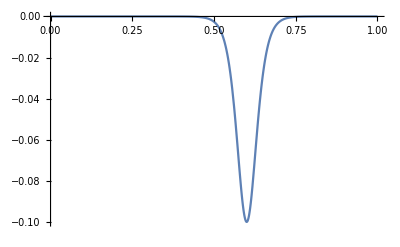

```mathematica
Plot[-β/Cosh[8π(r-rp)]^2 +β/Cosh[8π(r+rp)]^2/. {β->0.1,rp->0.6},{r,0,1}, PlotRange->Full]
```